```mathematica
SetDirectory[NotebookDirectory[]];Unprotect[Green];Green=RGBColor[0,0.777,0];

Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Off[NDSolve::"ndsz"](*vypnuti hlasky pri dosazeni horizontu*)
Off[NDSolve::maxit]
Off[NDSolve::"noout"]

fonty=15;fontyW={FontSize->15,Background->White};xInfinity=1000;VfontF=15;

ImSz=250;
ratio=250/300;

mujStyl={RotateLabel->False,Axes->False,Frame->True,ImageSize->ImSz,AspectRatio->1,BaseStyle->fontyW};

G=6.67300×10^-11;c=299792458 ;sM=1.98892×10^30 ;

tA[]:=(CasZ=SessionTime[];DateZ=DateString[{ "Start ","Time", " ","DayName", " ","Day", "/","Month"}];Date1=Date[];);
tB[]:=(CasK=SessionTime[];DateK=DateString[{ "Konec ","Time", " ","DayName", " ","Day", "/","Month"}];Date2=Date[];
Print[DateString[Date2-Date1,{ "TIME"," ","Time"," ","Day"}]<>"  #  "<>DateZ<>" / "<>DateK];);

(* 2D - polar coordinates *)
XX[r_,ϕ_]:=r Cos[ϕ];YY[r_,ϕ_]:=r Sin[ϕ];

(* 3D - spherical coordinates *)
XXX[r_,θ_,ϕ_]:=r Sin[θ] Cos[ϕ];
YYY[r_,θ_,ϕ_]:=r Sin[θ] Sin[ϕ];
ZZZ[r_,θ_,ϕ_]:=r Cos[θ];

ce="ℰ";cl="ℒ";cb="ℬ";

Veff[r_,B_,L_]:=(1-2/r)(1+(L/r-B r)^2);
VeffX[x_,y_,B_,L_]:=(1-2/(√(x^2+y^2)))(1+(L/x-B x)^2);Vflat[x_,B_,L_]:=(1+(L/x-B x)^2);EEflat[B_,L_]:=If[B L<0,√(1-4 B L),1];

LLm1[r_,B_]:=(B (-2+r) r^2-√2 √((-2+r) r^2))/(-2+r);LLm2[r_,B_]:=(B (-2+r) r^2+√2 √((-2+r) r^2))/(-2+r);
LLm3[r_,B_]:=-(B r^2 (2+r)+√2 √(r^2 (-2+r+4 B^2 r^3)))/(-2+r);LLm4[r_,B_]:=(-B r^2 (2+r)+√2 √(r^2 (-2+r+4 B^2 r^3)))/(-2+r);
fLL[r_,BB_]:=(-BB r^2+√(-3 r^2+r^3+4 BB^2 r^4-4 BB^2 r^5+BB^2 r^6))/(-3+r);fLLm[r_,BB_]:=(-BB r^2-√(-3 r^2+r^3+4 BB^2 r^4-4 BB^2 r^5+BB^2 r^6))/(-3+r);

LLmA[r_,B_]:=If[B<0,LLm3[r,B],LLm1[r,B]];LLmB[r_,B_]:=If[B<0,LLm4[r,B],LLm2[r,B]];

fLLnull[r_,B_]:=B r^2-√(r^2 (-3+r+4 B^2 r^2-4 B^2 r^3+B^2 r^4))+(-3+r) (-2 B r+((-2+r) r (3+2 B^2 r^2 (-4+3 r)))/(2 √(r^2 (-3+r+4 B^2 r^2-4 B^2 r^3+B^2 r^4))));
Lstar[r_,B_]:=B r^2;

FceJE[r_,L_,B_]:=-L^2 (-3+r)+r^2-2 B L r^2-B^2 r^4+B^2 r^5;

EBextrm[r_,L_,B_]:=(-L^2 (-3+r)+r^2-2 B L r^2-B^2 r^4+B^2 r^5);
fISCO[r_,B_]:=6-r+2 B^2 r(12-8r+9 r^2-2 r^3)+2 B (-6+r) √(2r +B^2 r^2 (4-4 r+5 r^2));
LEmin[r_,B_]:=-2 B r+√(2 r+4 B^2 r^2-4 B^2 r^3+5 B^2 r^4);

EEflat[B_,L_]:=If[B L<0,√(1-4 B L),1];OmegaC[BB_,LL_]:=(2BB)/EEflat[BB,LL];rmin[B_,L_]:=√Abs[L/B];
EEstr[B_,L_]:=√(1-√(4B/(L)));
EB2[r_,θ_,B_,L_]:=((-2+r ) (B^2 r^4+r^2 Csc[θ]^2-2 B L r^2 Csc[θ]^2+L^2 Csc[θ]^4) Sin[θ]^2)/r^3;
EB2extr[r_,B_,L_]:=L^2 (-3+r)+2 B L r^2+B^2 r^4-r^2-B^2 r^5;



fLL1[r_,BB_]:=(-BB r^2-√(-3 r^2+r^3+4 BB^2 r^4-4 BB^2 r^5+BB^2 r^6))/(-3+r);fLL2[r_,BB_]:=(-BB r^2+√(-3 r^2+r^3+4 BB^2 r^4-4 BB^2 r^5+BB^2 r^6))/(-3+r);

(* gives the trajectory *)
GiveMeTrajectorySCHW[BB_,LL_,R0_,θ0_,xEND_]:=(
Clear[r,pr,θ,pθ,ϕ,pϕ,EE];
RH=2;Rend =1.001RH;AA[r_]:=(1-2/r);
(*---- Metrics coefficients ----*)
 gtt[r_,θ_]:=-AA[r];grr[r_,θ_]:=1/AA[r];gθθ[r_,θ_]:= r^2;gϕϕ[r_,θ_]:=r^2 Sin[θ]^2;(* lower indicies *)
gUtt[r_,θ_]:=1/gtt[r,θ];gUrr[r_,θ_]:=1/grr[r,θ];gUθθ[r_,θ_]:= 1/gθθ[r,θ];gUϕϕ[r_,θ_]:=1/gϕϕ[r,θ]; (* upper indicies *)
(*---- Metrics coefficients ----*)
EE=√EB2[R0,θ0,BB,LL];
(*---- Hamiltonian a equations of motion ----*)
HoHo[r_,θ_,pr_,pθ_]:=1/2 gUrr[r,θ] pr^2+1/2 gUθθ[r,θ] pθ^2+1/2 gUtt[r,θ] EE^2+1/2 gUϕϕ[r,θ](LL -BB gϕϕ[r,θ])^2+1/2;
HamI=HoHo[r[τ],θ[τ],pr[τ],pθ[τ]];ERR[r_,θ_,pr_,pθ_]:=Abs[HoHo[r,θ,pr,pθ]];(* invariant for numerical integration and error function *)

DrHoHo[r_,θ_,pr_,pθ_]:=D[HoHo[r,θ,pr,pθ], r];DθHoHo[r_,θ_,pr_,pθ_]:=D[HoHo[r,θ,pr,pθ], θ];

Equations ={
r'[τ]   ==    gUrr[r[τ] ,θ[τ]]pr[τ],  pr'[τ]  == -DrHoHo[r[τ],θ[τ],pr[τ],pθ[τ]],
θ'[τ]   ==   gUθθ[r[τ] ,θ[τ]]pθ[τ],   pθ'[τ]  ==-DθHoHo[r[τ],θ[τ],pr[τ],pθ[τ]],
ϕ'[τ]   ==     (gUϕϕ[r[τ] ,θ[τ]]LL)-BB  (*This component is given by  \dot{\phi} / \tau = P^\phi = g^{\phi\phi} P_{\phi} = g^{\phi\phi} (L - BB g_{\phi\phi})  *)
};
IntCond ={r[0]    == R0, pr[0]   ==  0,θ[0]   == θ0, pθ[0]  == 0,ϕ[0]   == 0};
(*---- Hamiltonian a equations of motion ----*)

(*---- trajectory calculation ----*)
Metoda={"StiffnessSwitching", Method->{ {"Projection", Method->{"ExplicitRungeKutta","DifferenceOrder"->8},"Invariants"->HamI},Automatic}};
(* put your favourite numerical method here *)

draha=NDSolve[{Equations,IntCond},{r,pr,θ,pθ,ϕ},{τ,0,xEND},{Method->{"EventLocator","Event"->{r[τ]-Rend,r[τ]-xInfinity},"EventAction":>{Throw[ Null,"StopIntegration"],Throw[Null, "StopIntegration"]},"Method"->Metoda},{StartingStepSize->10^-1,MaxSteps->∞}}];
ipub=r/.draha[[1,1]];domain=ipub["Domain"];{begin,end} = domain[[1]];
(*---- trajectory calculation ----*)

(ϕ[τ]/.draha /.τ ->end)[[1]]

);

EB2[r_,θ_,B_,L_]:=((-2+r) (B^2 r^4+r^2 Csc[θ]^2-2 B L r^2 Csc[θ]^2+L^2 Csc[θ]^4) Sin[θ]^2)/r^3;
EB2extr[r_,B_,L_]:=L^2 (-3+r)+2 B L r^2+B^2 r^4-r^2-B^2 r^5;


(* fundamental frequencies for L < 0 (1) and L > 0 (2) *)

fLL1[r_,BB_]:=(-BB r^2-√(-3 r^2+r^3+4 BB^2 r^4-4 BB^2 r^5+BB^2 r^6))/(-3+r);fLL2[r_,BB_]:=(-BB r^2+√(-3 r^2+r^3+4 BB^2 r^4-4 BB^2 r^5+BB^2 r^6))/(-3+r);
fLL[r_,BB_]:=(-BB r^2+√(-3 r^2+r^3+4 BB^2 r^4-4 BB^2 r^5+BB^2 r^6))/(-3+r);

fLLnull[r_,B_]:=B r^2-√(r^2 (-3+r+4 B^2 r^2-4 B^2 r^3+B^2 r^4))+(-3+r) (-2 B r+((-2+r) r (3+2 B^2 r^2 (-4+3 r)))/(2 √(r^2 (-3+r+4 B^2 r^2-4 B^2 r^3+B^2 r^4))));

FF[r_,BB_]:=√(BB^2 r^2 (-2+r)^2 +r-3);

GG[r_,BB_]:=√(BB^2 r^2 (5 r^2-4r+4) +2r);

FceRLmin[B_]:=If[B<0,
Max[Select[r/.NSolve[B r^2 (2+r)-√2 √(r^2 (-2+r+4 B^2 r^3))+(-2+r) (-B r^2-2 B r (2+r)+(r (-4+3 r+20 B^2 r^3))/(√2 √(r^2 (-2+r+4 B^2 r^3))))==0,r],Element[#,Reals]&]],
Max[Select[r/.NSolve[-4 (√2+2 B √((-2+r) r^2))+r (√2+4 B √((-2+r) r^2))==0,r],Element[#,Reals]&]]
];
{FceRLmin[-0.1],FceRLmin[0.1]}
```

{3.34745,3.05828}

## fig. 01 - - - intro - - - trajektorie nenabite castice v rovine vs. trajektorie castice s nabojem

```mathematica
oblast3D={{-18,18},{-18,18},{-18,18}};arhead=0.01;

axes[x_,y_,z_,f_,a_]:=Graphics3D[Join[{Arrowheads[a]},Arrow[{{0,0,0},#}]&/@{{x,0,0},{0,-y,0},{0,0,z}},{Text[Style["x",FontSize->fonty],{0.9*x,-0.05*y,-0.05*z}],Text[Style["-y",FontSize->fonty],{0.1x,-0.85*y,0.05*z}],Text[Style["z",FontSize->fonty],{0.05*x,0.05*y,0.9*z}]}]];

R0=8;θ0=Pi/2-0.25;ϕ0=0;LL=fLL[R0,0]Sin[θ0];GiveMeTrajectorySCHW[0,LL,R0,θ0,112.397]
mRR=7;ltt=Pi/2-θ0;ptround=Table[{mRR Sin[tt],0,mRR Cos[tt]},{tt,Pi/2-ltt,θ0+ltt,ltt/4}];

stpt={XXX[R0,θ0,ϕ0],YYY[R0,θ0,ϕ0],ZZZ[R0,θ0,ϕ0]};
mRR=4;ptround=Table[{mRR Sin[tt],0,mRR Cos[tt]},{tt,0,θ0,θ0/7}];
pts=Table[Evaluate[{ XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]],  ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha][[1]],{τ,0,70,1}];
pic1=Show[
axes[9,9,8,0.05,arhead],
ParametricPlot3D[{ XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]],  ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotStyle->{Black,Dashed}],
Graphics3D[{{Black,Line[{{0,0,0},stpt}],Text[Style["r_0",fonty],{6.1,0,2.4}],BezierCurve[ptround],Text[Style["θ_0",fonty],{4.3,0,2.7}]},{Arrowheads[arhead],Black,Arrow[{{-3.26,-3.26,4},{-3,-3,8}}],Text[Style["B⃗",fonty],{-4,-4,6}],Text[Style["q = 0",fonty],{5,0,7}]},{LightGray,Opacity[0.9],Sphere[{0,0,0},2]},PointSize[0.03],Point[stpt],Arrowheads[1.5arhead],Thick,Arrow[BezierCurve[pts]]}],
{PlotRange->oblast3D,Boxed->False,PlotRange->oblast3D,ImageSize->ratio{400,250},Lighting->"Neutral",ViewPoint->{0.4,-0.5,0.35}}(*,AspectRatio->1*)
]
```

6.28318

-Graphics3D-

```mathematica
ratio=250/300
```

5/6

```mathematica
{400,250}
```

{400,250}

```mathematica
R0=8;θ0=Pi/2-0.25;ϕ0=0;LL=fLL[R0,0]Sin[θ0];BB=0;
{LL,GiveMeTrajectorySCHW[0,LL,R0,θ0,112.397]}
draha1=draha;begin1=begin;end1=end;
BB=0.2;LL2=LL+BB gϕϕ[R0,θ0];{LL2,GiveMeTrajectorySCHW[BB,LL2,R0,θ0,1065.894]}
draha2=draha;begin2=begin;end2=end;
```

{3.46649,6.28318}

{15.483,6.28318}

```mathematica
pic3=Show[
axes[9,9,8,0.05,arhead],
ParametricPlot3D[{ XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]],  ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha1,{τ,begin1,end1},PlotStyle->{Black,Dashed}],
ParametricPlot3D[{ XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]],  ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha2,{τ,begin2,end2},PlotStyle->{Black}],
Graphics3D[{{Arrowheads[arhead],Black,Arrow[{{-3.26,-3.26,4},{-3,-3,8}}],Text[Style["B⃗",fonty],{-4,-4,6}],Text[Style["q ≠ 0",fonty],{5,0,7}]},{LightGray,Opacity[0.9],Sphere[{0,0,0},2]},PointSize[0.03],Point[stpt]}],
{PlotRange->oblast3D,Boxed->False,PlotRange->oblast3D,ImageSize->ratio{400,250},Lighting->"Neutral",ViewPoint->{0.4,-0.5,0.35}}(*,AspectRatio->1*)
]
```

-Graphics3D-

```mathematica
pic=GraphicsRow[{pic1,pic3},Spacings->0]
```

-Graphics-

```mathematica
Export["01.eps",pic]
```

01.eps

## fig. 02 - - - Veff - - - efektivni potencial pro pohyb castice - eq. rovina a potencial v nekonecnu

```mathematica
Veff[r_,B_,L_]:=(1-2/r)(1+(L/r-B r)^2);Vflat[x_,B_,L_]:=(1+(L/x-B x)^2);rmin[B_,L_]:=√Abs[L/B];
```

{4.,4,4.47214,20.}

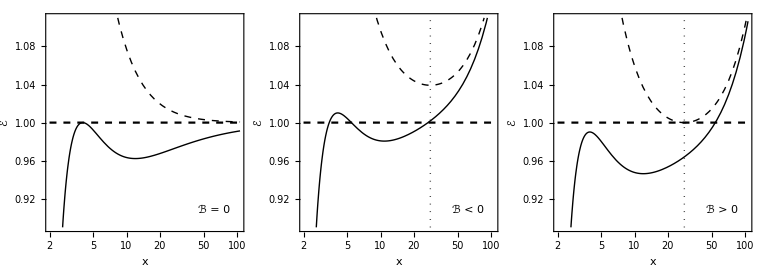

```mathematica
RR=12;LL=fLL[RR,0];BBx=0.005;Erange={0.89,1.11};rend=107;
{N[LL],LL,rmin[BB,LL],Abs[LL/BB]}
BB=0;pic1=LogLinearPlot[{1,√Vflat[x,BB,LL],√EB2[x,Pi/2,BB,LL]},{x,2,rend},FrameLabel->{"x",ce},RotateLabel->False,
PlotStyle->{{Black,Dashed},{Black,Thick,Dashed},{Black,Thick}},PlotRange->Erange,Frame->True,ImageSize->ImSz,AspectRatio->1,BaseStyle->fontyW,
Epilog->{Text[Row[{cb," = ",BB}],Scaled[{0.85,0.1}]]}];
BB=-BBx;pic2=LogLinearPlot[{1,√Vflat[x,BB,LL],√EB2[x,Pi/2,BB,LL]},{x,2,rend},FrameLabel->{"x",ce},RotateLabel->False,
PlotStyle->{{Black,Dashed},{Black,Thick,Dashed},{Black,Thick}},PlotRange->Erange,Frame->True,ImageSize->ImSz,AspectRatio->1,BaseStyle->fontyW,
Epilog->{Dotted,Line[{{Log[rmin[BB,LL]],Erange[[1]]},{Log[rmin[BB,LL]],Erange[[2]]}}],Text[Row[{cb," < 0"}],Scaled[{0.85,0.1}]]}];
BB=BBx;pic3=LogLinearPlot[{1,√Vflat[x,BB,LL],√EB2[x,Pi/2,BB,LL]},{x,2,rend},FrameLabel->{"x",ce},RotateLabel->False,
PlotStyle->{{Black,Dashed},{Black,Thick,Dashed},{Black,Thick}},PlotRange->Erange,Frame->True,ImageSize->ImSz,AspectRatio->1,BaseStyle->fontyW,
Epilog->{Dotted,Line[{{Log[rmin[BB,LL]],Erange[[1]]},{Log[rmin[BB,LL]],Erange[[2]]}}],Text[Row[{cb," > 0"}],Scaled[{0.85,0.1}]]}];
pic=GraphicsRow[{pic1,pic2,pic3},Spacings->0]
```

```mathematica
N[20 √2]
```

28.2843

```mathematica
Export["02.eps",pic];
```

## fig. 03 04 05 06 - - - pozice maxim a minim pro rJ a JE - - - B = 0.1 - - - i napocitane trajektorie pro konstanti L

```mathematica
mRange={{2,22},{0,14.5}};
FceRJpic[BB_]:=(
If[BB==0,
{Rmin,Lmin}={6,2 √3};{RLmin,LLmin}={4,4};{Rac,Lac}={23.63,3.73};{RLmin2,LLmin}={628,4};EEmaxFit= Fit[{{Rmin,Lmin},{Rac,Lac},{RLmin2,LLmin}}, {1,r,r^2}, r];
,
Rmin=Max[Select[r/.NSolve[fISCO[r,BB]==0,r],Element[#,Reals]&]];Lmin=LEmin[Rmin,BB];
RLmin=FceRLmin[BB];LLmin=LLmB[RLmin,BB];RLmin2=r/.NSolve[LLmin==LLmA[r,BB]][[1]];
Lac=(LLmin-Lmin)/2+Lmin;EEac2=EB2[Sort[Select[r/.NSolve[EBextrm[r,Lac,BB]],Element[#,Reals]&],Greater][[2]],Pi/2,BB,Lac];
Rac=Max[Select[r/.NSolve[EB2[r,Pi/2,BB,Lac]==EEac2,r],Element[#,Reals]&]];
EEmaxFit= Fit[{{Rmin,Lmin},{Rac,Lac},{RLmin2,LLmin}}, {1,r,r^2}, r];
];

pic=Show[
LogLinearPlot[-1,{x,2,20},Evaluate[mujStyl],PlotRange->mRange,FrameLabel->{"r",cl},ImagePadding->{{43,1},{43,1}},FrameTicks->{{2,3,5,7,10,15,20},Automatic,Automatic,Automatic},Epilog->{Text[Row[{cb," = ",BB}],Scaled[{0.83,0.1}]],Black,PointSize[0.02],Point[{Log[Rmin],Lmin}],Text["ℒ_ISCO",{Log[Rmin],Lmin-1}],kresli}],
LogLinearPlot[{fLL[r,BB],LLmB[r,BB]},{r,RLmin,22},Filling->{1->{2}},FillingStyle->LightGray,PlotStyle->{LightGray}],
LogLinearPlot[{LLmB[r,BB],EEmaxFit},{r,Rmin,RLmin2},Filling->{1->{2}},FillingStyle->LightGray,PlotStyle->{LightGray}],
LogLinearPlot[{fLL[r,BB],LLmA[r,BB]},{r,RLmin2,22},Filling->{1->{2}},FillingStyle->LightGray,PlotStyle->{LightGray}],
LogLinearPlot[{fLL[r,BB],fLLm[r,BB],LLmA[r,BB],LLmB[r,BB],LEmin[r,BB],Lstar[r,BB]},{r,0.001,60},Exclusions->{3},PlotPoints->200,PlotStyle->{{Black,Thick},{Black,Dashed,Thick},{Black,Dashed},{Black,Dashed},{Dotted,Black},{DotDashed,Black}}]
];
pic
);
```

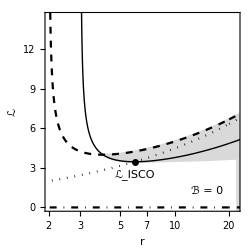
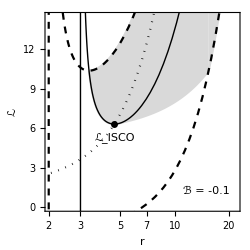
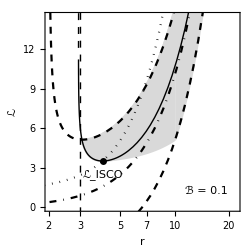

```mathematica
BB=0.1;typList={10,-1};kresli={};
{pic1=FceRJpic[0],pic2=FceRJpic[-BB],pic3=FceRJpic[BB]}
```

```mathematica
FceJEpic[BB_]:=(
If[BB==0,{Rmin,Lmin}={6,2 √3};{RLmin,LLmin}={4,4};,
Rmin=Max[Select[r/.NSolve[fISCO[r,BB]==0,r],Element[#,Reals]&]];Lmin=LEmin[Rmin,BB];RLmin=FceRLmin[BB];LLmin=LLmB[RLmin,BB];];
Eisco=√EB2[Rmin,Pi/2,BB,Lmin];

pic=Quiet[Plot[{If[L<LLmin,EEflat[BB,L],Null],(*2*) If[L>LLmin,EEflat[BB,L],Null],(*3*)
extrm=Select[r /. NSolve[EB2extr[r,BB,L]==0,r],Element[#,Reals]&&(#>2)&];
If[L>Lmin,If[L<LLmin,√EB2[Min[extrm],Pi/2,BB,L],Null],Null],(* 4 - max *)
extrm=Select[r /. NSolve[EB2extr[r,BB,L]==0,r],Element[#,Reals]&&(#>2)&];
If[L>Lmin,If[L>LLmin,√EB2[Min[extrm],Pi/2,BB,L],Null],Null],(* 5 - max *)
extrm=Select[r /. NSolve[EB2extr[r,BB,L]==0,r],Element[#,Reals]&&(#>2)&];
If[L>Lmin,√EB2[Max[extrm],Pi/2,BB,L],Null] ,(* 6 - min *)
If[BB>0,EEstr[BB,L],Null]
},{L,0.1,14.5},PlotRange->{{0,14.5},EErange},Filling->{3->{{5},LightGray},2->{{5},LightGray}},FrameLabel->{cl,ce},Evaluate[mujStyl],PlotStyle->{{Black,Dashed},{Black,Dashed},{Black,Thick},{Black,Thick},{Black,Thick},{Black,DotDashed}},ImagePadding->{{43,1},{43,1}},Epilog->{Black,PointSize[0.02],Point[{Lmin,Eisco}],Text["ℰ_ISCO",{Lmin,Eisco-0.05(EErange[[2]]-EErange[[1]])}],Text[Row[{cb," = ",BB}],Scaled[{0.83,0.1}]],kresli}]];
pic
);
```

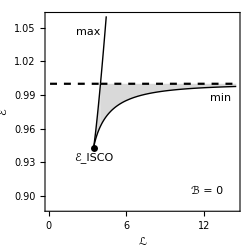
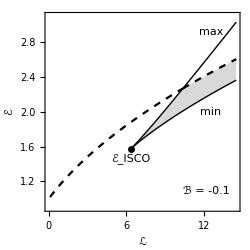
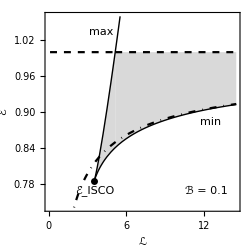

```mathematica
BB=0.1;{
EErange={0.89,1.06};kresli={Text["min",Scaled[{0.9,0.57}]],Text["max",Scaled[{0.22,0.9}]]};pic1=FceJEpic[0],
EErange={0.9,3.1};kresli={Text["min",Scaled[{0.85,0.5}]],Text["max",Scaled[{0.85,0.9}]]};pic2=FceJEpic[-BB],
EErange={0.74,1.06};kresli={Text["min",Scaled[{0.85,0.45}]],Text["max",Scaled[{0.29,0.9}]]};pic3=FceJEpic[BB]}
```

```mathematica
oblast2D={{-11,11},{-11,11}};ImSz=ratio 250;
LiazTra[no_]:=(
ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotStyle->{Black},Frame->True,BaseStyle->15,PlotRange->oblast2D,Epilog->{Text[symbol,Scaled[{0.1,0.9}]],Text[Row[{"r_0=",R0,",  ",ce,"=",Round[EE,0.001]}],Scaled[{0.5,0.1}]],Text[no,Scaled[{0.9,0.9}]],PointSize[0.02],Point[{(R0)Sin[Pi/2],0}],Black,Dotted,Circle[{0,0},RRmin],LightGray,Disk[{0,0},RH]},FrameLabel->{"x","y"},RotateLabel->False,Axes->False,ImageSize->ImSz]
);
```

### B = 0

```mathematica
{kresli={};pic1=FceRJpic[0],
EErange={0.89,1.06};kresli={Text["min",Scaled[{0.9,0.57}]],Text["max",Scaled[{0.22,0.9}]]};fig1=FceJEpic[0]}
```

{-Graphics-,-Graphics-}

### B < 0

```mathematica
figex={{-0.1,9.5,7.7,1.8},{-0.1,9.5,8.3,1.8},{0.1,9.5,8,0.9},{-0.1,16,7.1,3}};
```

```mathematica
typList={{Log[3],8},{Log[5],8},{Log[6.79],8},{Log[12],8}};
typListX={{Log[9.5],7.7},{Log[9.5],8.3},{Log[16],7.1}};
typListE={{8,1.807},{8,1.802},{8,1.772},{8,1.933}};
typListEX={{7.7,1.8},{8.3,1.8},{7.1,3}};
```

```mathematica
BB=-0.1;symbol="-";
```

```mathematica
RRmin=Max[Select[r/.NSolve[fLL[r,BB]==8,r],Element[#,Reals]&]]
```

6.78411

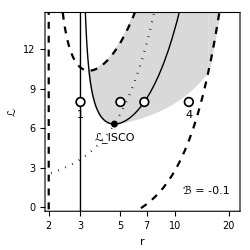
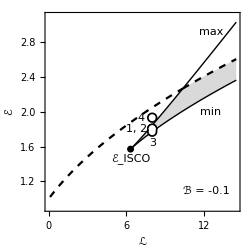

```mathematica
{kresli={PointSize[0.03],Point[typList],White,PointSize[0.02],Point[typList],Black,
(*Text["a",{typListX[[1,1]],typListX[[1,2]]-0.7}],Text["b",{typListX[[2,1]],typListX[[2,2]]+0.7}],Text["d",{typListX[[3,1]],typListX[[3,2]]-1}],*)
Text[1,{typList[[1,1]],7}],Text[4,{typList[[4,1]],7}]};pic2=FceRJpic[BB],
kresli={Text["min",Scaled[{0.85,0.5}]],Text["max",Scaled[{0.85,0.9}]],PointSize[0.03],Point[typListE],White,PointSize[0.02],Point[typListE],
Black,Text[3,{8,typListE[[3,2]]-0.13}],Text["1, 2",{6.8,typListE[[2,2]]}],Text[4,{7.1,typListE[[4,2]]}]};EErange={0.9,3.1};fig2=FceJEpic[BB]}
```

```mathematica
NSolve[fLL[r,BB]==8,r]
```

{{r→6.78411},{r→3.59132}}

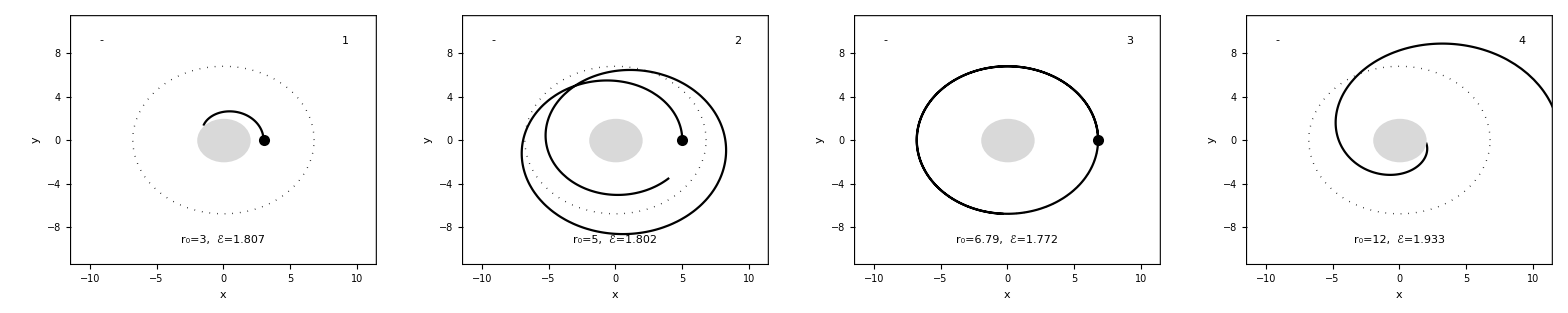

```mathematica
typList={{Log[3],8},{Log[5],8},{Log[6.79],8},{Log[12],8}};
typListE={{8,1.807},{8,1.802},{8,1.772},{8,1.933}};
tra=40;tra2=GraphicsGrid[{
{ii=1;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=2;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=3;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=4;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii]}},Spacings->2]
```

```mathematica
Export["05.eps",tra2];
```

### B > 0 (1-7)

```mathematica
BB=0.1;symbol="+";
```

```mathematica
RRmin=Max[r/.NSolve[fLL[r,BB]==4.5,r]]
```

5.76621

```mathematica
typList={{Log[3],4.5},{Log[4],4.5},{Log[5],4.5},{Log[5.77],4.5},{Log[6.5],4.5},{Log[7.5],4.5},{Log[9],4.5}};
typListE={{4.5,0.902},{4.5,0.873},{4.5,0.834},{4.5,0.825},{4.5,0.833},{4.5,0.866},{4.5,0.950}};
```

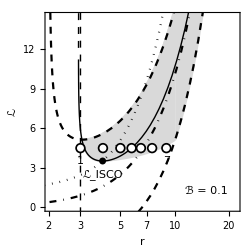
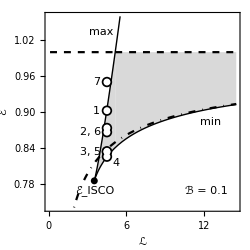

```mathematica
{kresli={PointSize[0.03],Point[typList],White,PointSize[0.02],Point[typList],Black,Text[1,{typList[[1,1]],3.5}],Text[7,{typList[[7,1]],3.5}]};pic3=FceRJpic[BB],
kresli={Text["min",Scaled[{0.85,0.45}]],Text["max",Scaled[{0.29,0.9}]],PointSize[0.03],Point[typListE],White,PointSize[0.02],Point[typListE],
Black,Text[1,{3.7,typListE[[1,2]]}],Text["3, 5",{3.2,typListE[[5,2]]}],Text["2, 6",{3.2,typListE[[6,2]]}],Text[4,{5.2,typListE[[4,2]]-0.01}],Text[Style[" 7 ",Background->White],{3.7,typListE[[7,2]]}]};EErange={0.74,1.06};fig3=FceJEpic[BB]}
```

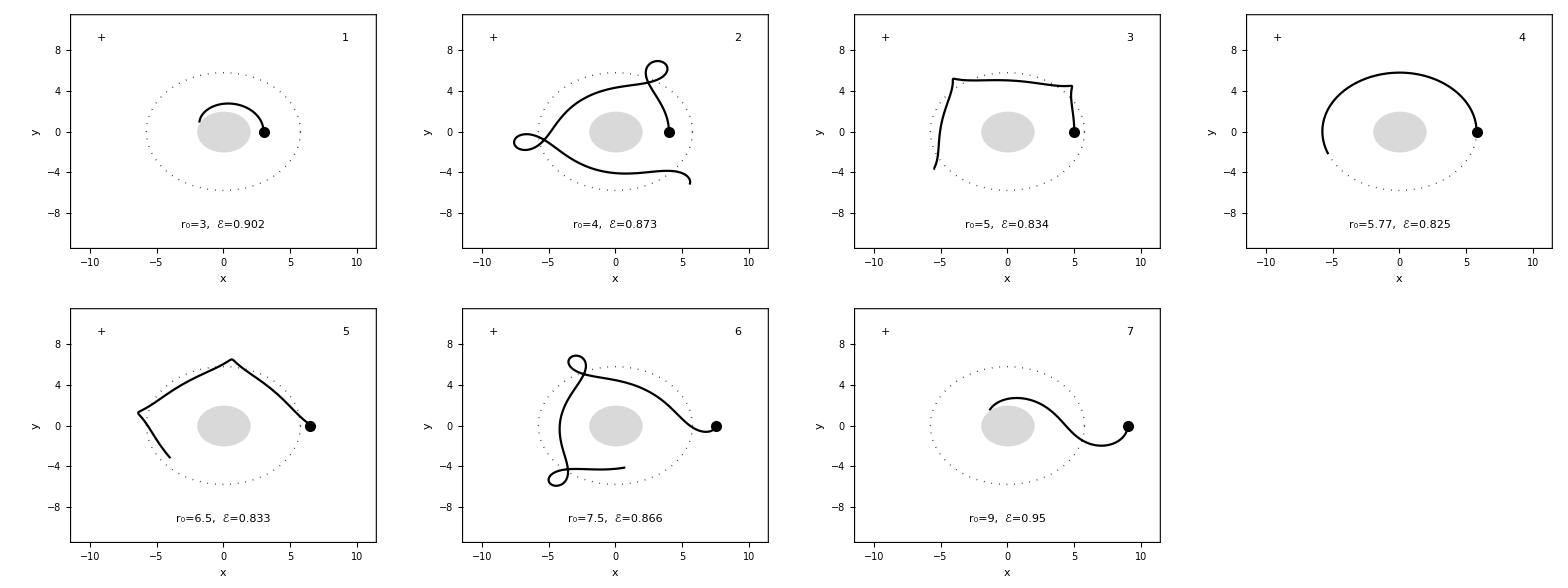

```mathematica
tra=100;tra3=GraphicsGrid[{
{ii=1;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=2;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=3;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=4;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii]},{ii=5;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=6;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=7;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii]
(*ii=8;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii]*)}},Spacings->2]
```

```mathematica
Export["06.eps",tra3];
```

### B > 0 (1-8)

```mathematica
Vyhodit typ 8???
```

p?test is a pattern object that stands for any expression that matches p, and on which the application of test gives True.

Attributes[PatternTest]={HoldRest,Protected}

8 Null typ Vyhodit

```mathematica
NSolve[fLL[r,BB]==4.5,r]
```

{{r→5.76621},{r→3.15449}}

```mathematica
typListE[[8,2]]
```

Part::partw: Part 8 of {{4.5,0.902},{4.5,0.873},{4.5,0.834},{4.5,0.825},{4.5,0.833},{4.5,0.866},{4.5,0.95}} does not exist.

{{4.5,0.902},{4.5,0.873},{4.5,0.834},{4.5,0.825},{4.5,0.833},{4.5,0.866},{4.5,0.95}}⟦8,2⟧

```mathematica
{kresli={PointSize[0.03],Point[typList],White,PointSize[0.02],Point[typList],Black,Text[1,{typList[[1,1]],3.5}],Text[8,{typList[[8,1]],3.5}]};FceRJpic[BB],
kresli={PointSize[0.03],Point[typListE],White,PointSize[0.02],Point[typListE],
Black,Text[1,{3.7,typListE[[1,2]]}],Text["3, 5",{3.2,typListE[[5,2]]}],Text["2, 6",{3.2,typListE[[6,2]]}],Text[4,{5.2,typListE[[4,2]]-0.01}],Text[7,{3.7,typListE[[7,2]]}],Text[8,{4.5,typListE[[8,2]]-0.03}]};EErange={0.74,1.11};FceJEpic[BB]}
```

Part::partw: Part 8 of {{Log[3],4.5},{Log[4],4.5},{Log[5],4.5},{1.75267,4.5},{1.8718,4.5},{2.0149,4.5},{Log[9],4.5}} does not exist.

Part::partw: Part 8 of {{4.5,0.902},{4.5,0.873},{4.5,0.834},{4.5,0.825},{4.5,0.833},{4.5,0.866},{4.5,0.95}} does not exist.

{-Graphics-,-Graphics-}

```mathematica
typList={{Log[3],4.5},{Log[4],4.5},{Log[5],4.5},{Log[5.77],4.5},{Log[6.5],4.5},{Log[7.5],4.5},{Log[9],4.5},{Log[11],4.5}};
typListE={{4.5,0.902},{4.5,0.873},{4.5,0.834},{4.5,0.825},{4.5,0.833},{4.5,0.866},{4.5,0.950},{4.5,1.099}};
```

```mathematica
LiazTra[no_]:=(
ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotStyle->{Black},Frame->True,BaseStyle->15,PlotRange->oblast2D,Epilog->{Text[Row[{"r_0=",R0,",  ",ce,"=",Round[EE,0.001]}],Scaled[{0.5,0.1}]],Text[no,Scaled[{0.9,0.9}]],PointSize[0.02],Point[{(R0)Sin[Pi/2],0}],Black,Dotted,Circle[{0,0},R0],LightGray,Disk[{0,0},RH]},FrameLabel->{"x","y"},RotateLabel->False,Axes->False,ImageSize->ImSz]
);
```

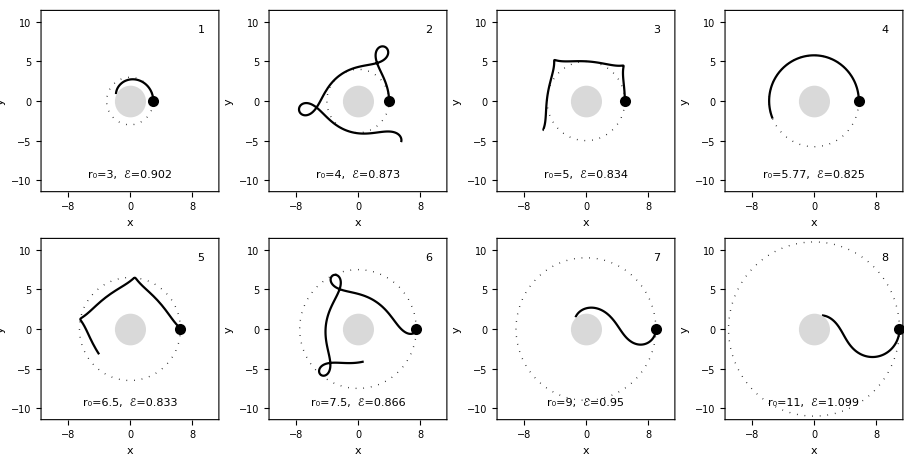

```mathematica
tra=100;GraphicsGrid[{
{ii=1;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=2;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=3;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=4;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii]},{ii=5;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=6;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=7;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii],
ii=8;{R0,LL}={Exp[typList[[ii,1]]],typList[[ii,2]]};GiveMeTrajectorySCHW[BB,LL,R0,Pi/2,tra];pic=LiazTra[ii]}}]
```

### ALL

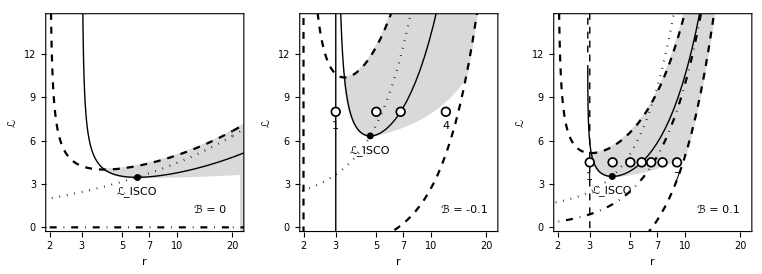

```mathematica
pic=GraphicsRow[{pic1,pic2,pic3},Spacings->0]
Export["03.eps",pic];
```

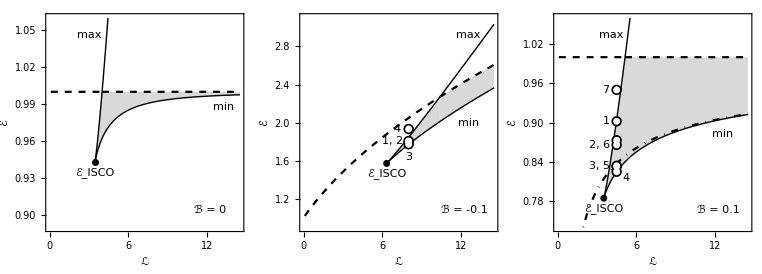

```mathematica
fig=GraphicsRow[{fig1,fig2,fig3},Spacings->0]
Export["04.eps",fig];
```

## fig. 07 priklady ruznych trajektorii pohybu. . . trajektorie . . .

```mathematica
TatraTra[]:=(
(*Print[(R0+ddRR)Sin[Pi/2+ddTT]];*)
GraphicsRow[{pic1=ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotStyle->{Black},Frame->True,BaseStyle->15,PlotRange->oblast2D,Epilog->{PointSize[0.02],Point[{(R0+ddRR)Sin[Pi/2+ddTT],0}],LightGray,Disk[{0,0},RH]},FrameLabel->{"x","y"},RotateLabel->False,Axes->False,ImageSize->ImSz],
pic2=ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]],ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotStyle->{Black},Frame->True,BaseStyle->15,PlotRange->oblast2D,Prolog->{LightGray,Disk[{0,0},RH]},FrameLabel->{"x","z"},RotateLabel->False,Axes->False,ImageSize->ImSz,Epilog->{Text[Row[{cb,"=",BB,", ",cl,"≐",Round[LL,0.1],", ",ce,"≐",Round[EE,0.1]}],Scaled[{0.5,0.9}]],
PointSize[0.02],Point[{XXX[R0+ddRR,Pi/2+ddTT,0],ZZZ[R0+ddRR,Pi/2+ddTT,0]}],
Text[Row[{"r_0≐",Round[R0+ddRR,0.1],", θ_0≐",Round[Pi/2+ddTT,0.1]}],Scaled[{0.5,0.1}]]}],
pic3=Show[ParametricPlot[ {XXX[r[τ],θ[τ],0],ZZZ[r[τ],θ[τ],0] }/.draha,{τ,begin,fix end},PlotStyle->{Black},Frame->True,BaseStyle->15,PlotRange->{{0,oblast1D[[2]]},{oblast1D[[1]]/2,oblast1D[[2]]/2}},Prolog->{LightGray,Disk[{0,0},RH]},FrameLabel->{"x","z"},RotateLabel->False,Axes->False,ImageSize->ImSz,Epilog->{PointSize[0.02],Point[{XXX[R0+ddRR,Pi/2+ddTT,0],ZZZ[R0+ddRR,Pi/2+ddTT,0]}]}],
ContourPlot[EB2[√(xx^2+zz^2),ArcTan[xx/zz],BB,LL]==EE^2,{xx,0,oblast1D[[2]]},{zz,oblast1D[[1]]/2,oblast1D[[2]]/2},ContourStyle->{{Black,Dashed}}]],
pic4=Show[ParametricPlot3D[{ XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]],  ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotRange->oblast3D,(*AxesLabel->{"x","y","z"},*)BoxStyle->{Black},PlotStyle->{Black},ViewPoint->{0,-3,1},Ticks->None,ImageSize->ImSz,Epilog->{Text[Framed[Row[{cb,"=",BB,", ",cl,"≐",Round[LL,0.1],", ",ce,"≐",Round[EE,0.1]}]],Scaled[{0.5,0.9}]]}],
Graphics3D[{{Black,Opacity[.15],Sphere[{0,0,0},2]},
(*{Arrowheads[arhead],Black,Arrow[{{8,4,2},{7.75,3.7,6}}],Text[Style["B⃗",fonty],{6.7,4,4.5}]},*)
{Black,PointSize[0.02],Point[{XXX[R0+ddRR,Pi/2+ddTT,0],YYY[R0+ddRR,Pi/2+ddTT,0],ZZZ[R0+ddRR,Pi/2+ddTT,0]}]}}]]
}]
);

ImSz=ratio 250;oblast1D={-11,11};oblast2D={oblast1D,oblast1D};oblast3D={oblast1D,oblast1D,oblast1D};
```

```mathematica
BB=0.1;R0=8.5;ddRR=1;ddTT=ddRR/25;LL=fLL2[R0,BB];fix=0.3;GiveMeTrajectorySCHW[BB,LL,R0+ddRR,Pi/2+ddTT,550];pic=TatraTra[]
```

-Graphics-

```mathematica
Export["07c.eps",GraphicsColumn[{pic1,pic2,pic3,pic4}]];
```

```mathematica
BB=-0.1;R0=7;ddRR=2.5;ddTT=ddRR/50;LL=fLL2[R0,BB];fix=1;GiveMeTrajectorySCHW[BB,LL,R0+ddRR,Pi/2+ddTT,100];pic=TatraTra[]
```

-Graphics-

```mathematica
Export["07b.eps",GraphicsColumn[{pic1,pic2,pic3,pic4}]];
```

```mathematica
BB=-0.1;R0=6.5;ddRR=3;ddTT=ddRR/50;LL=fLL2[R0,BB];fix=1;GiveMeTrajectorySCHW[BB,LL,R0+ddRR,Pi/2+ddTT,100];pic=TatraTra[]
```

-Graphics-

```mathematica
Export["07a.eps",GraphicsColumn[{pic1,pic2,pic3,pic4}]];
```

```mathematica
TatraTra2[]:=(
(*Print[(R0+ddRR)Sin[Pi/2+ddTT]];*)
GraphicsRow[{pic1=ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotStyle->{Black},Frame->True,BaseStyle->15,PlotRange->oblast2D,Epilog->{PointSize[0.02],Point[{(R0+ddRR)Sin[Pi/2+ddTT],0}],LightGray,Disk[{0,0},RH]},FrameLabel->{"x","y"},RotateLabel->False,Axes->False,ImageSize->ImSz],
pic2=ParametricPlot[ {XXX[r[τ],θ[τ],ϕ[τ]],ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotStyle->{Black},Frame->True,BaseStyle->15,PlotRange->oblast2D,Prolog->{LightGray,Disk[{0,0},RH]},FrameLabel->{"x","z"},RotateLabel->False,Axes->False,ImageSize->ImSz,Epilog->{Text[Row[{cb,"=",BB,", ",cl,"≐",Round[LL,0.1],", ",ce,"≐",Round[EE,0.1]}],Scaled[{0.5,0.9}]],
PointSize[0.02],Point[{XXX[R0+ddRR,Pi/2+ddTT,0],ZZZ[R0+ddRR,Pi/2+ddTT,0]}],
Text[Row[{"r_0≐",Round[R0+ddRR,0.1],", θ_0≐",Round[Pi/2+ddTT,0.1]}],Scaled[{0.5,0.1}]]}],
pic3=Show[ParametricPlot[ {XXX[r[τ],θ[τ],0],ZZZ[r[τ],θ[τ],0] }/.draha,{τ,begin,fix end},PlotStyle->{Black},Frame->True,BaseStyle->15,PlotRange->{{0,oblast1D[[2]]},{oblast1D[[1]]/2,oblast1D[[2]]/2}},Prolog->{LightGray,Disk[{0,0},RH]},FrameLabel->{"x","z"},RotateLabel->False,Axes->False,ImageSize->ImSz,Epilog->{PointSize[0.02],Point[{XXX[R0+ddRR,Pi/2+ddTT,0],ZZZ[R0+ddRR,Pi/2+ddTT,0]}]}],
ContourPlot[EB2[√(xx^2+zz^2),ArcTan[xx/zz],BB,LL]==EE^2,{xx,0,oblast1D[[2]]},{zz,oblast1D[[1]]/2,oblast1D[[2]]/2},ContourStyle->{{Black,Dashed}}]],
pic4=Show[ParametricPlot3D[{ XXX[r[τ],θ[τ],ϕ[τ]], YYY[r[τ],θ[τ],ϕ[τ]],  ZZZ[r[τ],θ[τ],ϕ[τ]] }/.draha,{τ,begin,end},PlotRange->oblast3D,(*AxesLabel->{"x","y","z"},*)BoxStyle->{Black},PlotStyle->{Black},ViewPoint->{0,-3,1},Ticks->None,ImageSize->ImSz,Epilog->{Text[Framed[Row[{cb,"=",BB,", ",cl,"≐",Round[LL,0.1],", ",ce,"≐",Round[EE,0.1]}]],Scaled[{0.5,0.9}]]}],
Graphics3D[{{Black,Opacity[.15],Sphere[{0,0,0},2]},
(*{Arrowheads[arhead],Black,Arrow[{{8,4,2},{7.75,3.7,6}}],Text[Style["B⃗",fonty],{6.7,4,4.5}]},*)
{Black,PointSize[0.02],Point[{XXX[R0+ddRR,Pi/2+ddTT,0],YYY[R0+ddRR,Pi/2+ddTT,0],ZZZ[R0+ddRR,Pi/2+ddTT,0]}]}}]]
}]
);
```

```mathematica
ImSz=ratio 250;oblast1D={-42.5,42.5};oblast2D={oblast1D,oblast1D};oblast3D={oblast1D,oblast1D,oblast1D};
BB=-0.1;R0=6;ddRR=10;ddTT=ddRR/7.1;LL=fLL2[R0,BB];fix=1;GiveMeTrajectorySCHW[BB,LL,R0+ddRR,Pi/2+ddTT,90];pic=TatraTra2[]
```

-Graphics-

```mathematica
Export["07d.eps",GraphicsColumn[{pic1,pic2,pic3,pic4}]];
```

```mathematica
ImSz=250;oblast1D={-425,425};oblast2D={oblast1D,oblast1D};oblast3D={oblast1D,oblast1D,oblast1D};
BB=-0.1;R0=12;ddRR=13.1;ddTT=ddRR/9.8;LL=fLL2[R0,BB];fix=1;GiveMeTrajectorySCHW[BB,LL,R0+ddRR,Pi/2+ddTT,90];pic=TatraTra2[]
```

-Graphics-

## fig. 08 - - - small oscilations - intro fig

```mathematica
oblast3D={{-16,20},{-10,10},{-4,7}};arhead=0.01;

axes[x_,y_,z_,f_,a_]:=Graphics3D[Join[{colour,Arrowheads[a]},Arrow[{{0,0,0},#}]&/@{{x,0,0},{0,-y,0},{0,0,z}},{Text[Style["",FontSize->fonty],{0.9*x,-0.05*y,-0.05*z}],Text[Style["",FontSize->fonty],{0.2x,-0.9*y,0.05*z}],Text[Style["",FontSize->fonty],{0.05*x,0.05*y,0.9*z}]}]];

R0=10;θ0=Pi/2;stpt={XXX[R0,θ0,0],YYY[R0,θ0,0],ZZZ[R0,θ0,0]};

colour=Lighter[Gray,0.5];lid=0.25;colour2=Black;
pic=Show[
axes[7,7,7,0.05,arhead],
ParametricPlot3D[{ XXX[R0,θ0,ϕ], YYY[R0,θ0,ϕ],  ZZZ[R0,θ0,ϕ] },{ϕ,0+lid,2Pi-lid},PlotStyle->{Thick,colour}],
ParametricPlot3D[{ XXX[R0,θ0,ϕ], YYY[R0,θ0,ϕ],  ZZZ[R0,θ0,ϕ] },{ϕ,-lid,lid},PlotStyle->{Thick,Black}],
ParametricPlot3D[{ XXX[1.5,Pi/2,ϕ]-3.1, YYY[1.5,Pi/2,ϕ]-3.1,  ZZZ[1.5,Pi/2,ϕ]+4},{ϕ,0,2Pi},PlotStyle->{Thick,colour2}],
(*ParametricPlot3D[{ XXX[R0,θ0,ϕ], YYY[R0,θ0,ϕ],  ZZZ[R0,θ0,ϕ]+1 },{ϕ,0,2Pi},PlotStyle->{Dotted,Black}],
ParametricPlot3D[{ XXX[R0,θ0,ϕ], YYY[R0,θ0,ϕ],  ZZZ[R0,θ0,ϕ] -1},{ϕ,0,2Pi},PlotStyle->{Dotted,Black}],*)
Graphics3D[{
{colour2,Text[Style["ω_L",fonty,Background->White],{-1.5,-1,4.5}]},
{Arrowheads[arhead],Black,Arrow[{{-3.2,-3.2,3},{-3,-3,7}}],Text[Style["B⃗",fonty],{-4,-4,6}]},
{Black,Arrowheads[arhead],Text[Style["ω_ϕ",{fonty,Background->White}],{R0+1.2,0,1.9}],Arrow[{{ XXX[R0,θ0,-lid], YYY[R0,θ0,-lid],  ZZZ[R0,θ0,-lid]},{ XXX[R0,θ0,-lid-0.03], YYY[R0,θ0,-lid-0.03],  ZZZ[R0,θ0,-lid-0.03]}}],Arrow[{{ XXX[R0,θ0,lid], YYY[R0,θ0,lid],  ZZZ[R0,θ0,lid]},{ XXX[R0,θ0,lid+0.03], YYY[R0,θ0,lid+0.03],  ZZZ[R0,θ0,lid+0.03]}}]},
{Black,Thick,Arrowheads[{-1.1arhead,1.1arhead}],Arrow[{{R0-1.5,0,0},{R0+1.5,0,0}}],Text[Style["ω_r",fonty,Background->White],{12.2,0,0.3}]},
{Black,Thick,Arrowheads[{-1.1arhead,1.1arhead}],Arrow[{{R0,0,-1.5},{R0,0,1.5}}],Text[Style["ω_θ",{fonty,Background->White}],{R0+0.1,0,-1.8}]},{colour,Opacity[0.1],Sphere[{0,0,0},2]}}],
{PlotRange->oblast3D,Boxed->False,PlotRange->oblast3D,ImageSize->{400,200},Lighting->"Neutral",ViewPoint->{0.4,-0.5,0.25}}(*,AspectRatio->1*)
]
```

-Graphics3D-

```mathematica
Export["08.eps",pic]
```

08.eps

## fig. 09 ---/ locally measured fundamental frequencies (ω_r,ω_θ,ω_K) /---

```mathematica
fLL[r_,BB_]:=(-BB r^2+√(-3 r^2+r^3+4 BB^2 r^4-4 BB^2 r^5+BB^2 r^6))/(-3+r); (* Gives angular momentum fo charget particle on circular orbit with radius r in homo.mag.field B && L > 0 *)

fωK[r_,BB_]:=1/(2Pi)(1/r^2 fLL[r,BB]-BB);
fωr[r_,BB_]:=1/(2Pi)√((3 fLL[r,BB]^2 (-2+r)^3+(-2 r(-2+r) (fLL[r,BB]^2+r^2-2 BB fLL[r,BB] r^2+BB^2 r^4)+BB^2  r^4(-2+r)^3))/((-2+r)^2 r^5));fωt[r_,BB_]:=1/(2Pi)√(-BB^2+fLL[r,BB]^2/r^4);

fωK[r_,BB_]:=(1/r^2 fLL[r,BB]-BB);
fωr[r_,BB_]:=√((3 fLL[r,BB]^2 (-2+r)^3+(-2 r(-2+r) (fLL[r,BB]^2+r^2-2 BB fLL[r,BB] r^2+BB^2 r^4)+BB^2  r^4(-2+r)^3))/((-2+r)^2 r^5));fωt[r_,BB_]:=√(-BB^2+fLL[r,BB]^2/r^4);
FceNull[r_,BB_]:=(18-9 r+r^2-48 BB^2 r^2+68 BB^2 r^3-30 BB^2 r^4+4 BB^2 r^5+(12 BB-2 BB r ) √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))); (* zero points for fωr function *)
```

```mathematica
Expand[3 L^2 (-2+r)^3+(-2 r(-2+r) (L^2+r^2-2 B L r^2+B^2 r^4)+B^2  r^4(-2+r)^3)]
```

-24 L^2+40 L^2 r-20 L^2 r^2+4 r^3-8 B L r^3+3 L^2 r^3-2 r^4-8 B^2 r^4+4 B L r^4+16 B^2 r^5-8 B^2 r^6+B^2 r^7

```mathematica
Simplify[1/((-2+r)^2 r^5)(3 L^2 (-2+r)^3+(-2 r(-2+r) (L^2+r^2-2 B L r^2+B^2 r^4)+B^2  r^4(-2+r)^3))
-1/((-2+r) r^5)(3 L^2 (-2+r)^2+(-2 r (L^2+r^2-2 B L r^2+B^2 r^4)+B^2  r^4(-2+r)^2))]
```

0

```mathematica
Simplify[1/((-2+r) r^5)(3 L^2 (-2+r)^2+(-2 r (L^2+r^2-2 B L r^2+B^2 r^4)+B^2  r^4(-2+r)^2))-1/((r-2) r^5)((r-2)^2(B^2 r^4+3 L^2)-2 r (B^2 r^4-2 B L r^2+L^2+r^2))]
```

0

```mathematica
Simplify[1/((r-2) r^5)((r-2)^2(B^2 r^4+3 L^2)-2 r (B^2 r^4-2 B L r^2+L^2+r^2))-1/((r-2) r^5)((r-2)^2(B^2 r^4+3 L^2)-2 r (B r^2-L)^2-2 r^3)]
```

0

```mathematica
FullSimplify[((r-2)^2(B^2 r^4+3 L^2)-2 r (B r^2-L)^2-2 r^3)]
```

-2 r^3-2 r (L-B r^2)^2+(-2+r)^2 (3 L^2+B^2 r^4)

```mathematica
Limit[{fωK[r,B],fωt[r,B],fωr[r,B]},r->Infinity]
```

{-B+√(B^2),0,2 √(B^2)}

```mathematica
{fLL[6,0],fLL[12,0]}
```

{2 √3,4}

```mathematica
BB1=0;BB=0.1;BB2=-0.1;BB3=0.1;
Clear[r];
rBB1=Max[Select[r/.NSolve[FceNull[r,BB1]==0,r],Element[#,Reals]&]];
rBB2=Max[Select[r/.NSolve[FceNull[r,BB2]==0,r],Element[#,Reals]&]];
rBB3=Max[Select[r/.NSolve[FceNull[r,BB3]==0,r],Element[#,Reals]&]];
{rBB1,rBB2,rBB3}
```

{6.,4.63195,3.98268}

```mathematica
colour=Lighter[Gray,0.7];lid=0.25;colour2=(*Darker[Yellow,0.05]*)Brown;
```

```mathematica
∄
```

```mathematica
coK={Black,Dashed};coR={Black};coT={Black,Thick};coL={Black,DotDashed};
```

```mathematica
Legenda={
{lin=0.85;Black,Text["ω_r",Scaled[{0.1,lin+0.04}]],Line[{Scaled[{0.05,lin}],Scaled[{0.15,lin}]}]},
{lin=0.75;Black,Thick,Text["ω_θ",Scaled[{0.1,lin+0.04}]],Line[{Scaled[{0.05,lin}],Scaled[{0.15,lin}]}]},
{lin=0.65;Black,Dashed,Text["ω_ϕ",Scaled[{0.1,lin+0.04}]],Line[{Scaled[{0.05,lin}],Scaled[{0.15,lin}]}]},
{lin=0.55;Black,DotDashed,Text["ω_L",Scaled[{0.1,lin+0.04}]],Line[{Scaled[{0.05,lin}],Scaled[{0.15,lin}]}]}
};
```

```mathematica
ImSz=250;
```

```mathematica
OMmax=0.041;BB=0.001;
fceOMOMO[BB_,OMmax_]:=(
rBBm=Max[Select[r/.NSolve[FceNull[r,-BB]==0,r],Element[#,Reals]&]];
rBBp=Max[Select[r/.NSolve[FceNull[r,BB]==0,r],Element[#,Reals]&]];

GraphicsRow[{
LogLinearPlot[{fωK[r,0],fωr[r,0],fωt[r,0]},{r,6,50},PlotRange->{{2,55},{0,OMmax}},Frame->True,Axes->False,AspectRatio->1,ImageSize->ImSz,FrameLabel->{"r","ω"},RotateLabel->False,BaseStyle->15,PlotStyle->{coK,coR,coT},ImagePadding->{{50,2},{45,2}},Epilog->{Text[Style["ISCO",Gray],Scaled[{0.33,0.9}]],{Dotted,Line[{{Log[6],0},{Log[6],OMmax}}]},Text[Row[{ cb," = ",0}],Scaled[{0.8,0.9}]],Text["ω_ϕ=ω_θ,\n ω_L ∄",Scaled[{0.8,0.7}]],Legenda}],

LogLinearPlot[{fωK[r,-BB],fωr[r,-BB],fωt[r,-BB],2Abs[-BB]},{r,rBBm,50},PlotRange->{{2,55},{0,OMmax}},Frame->True,Axes->False,AspectRatio->1,ImagePadding->{{50,2},{45,2}},ImageSize->ImSz,FrameLabel->{"r","ω"},RotateLabel->False,BaseStyle->15,PlotStyle->{coK,coR,coT,coL},Epilog->{{Dotted,Line[{{Log[rBBm],0},{Log[rBBm],OMmax}}]},Text[Row[{ cb," = ",-BB}],Scaled[{0.8,0.9}]],Legenda}],

LogLinearPlot[{fωK[r,BB],fωr[r,BB],fωt[r,BB],2Abs[BB]},{r,rBBp,50},PlotRange->{{2,55},{0,OMmax}},Frame->True,Axes->False,AspectRatio->1,ImagePadding->{{50,2},{45,2}},ImageSize->ImSz,FrameLabel->{"r","ω"},RotateLabel->False,BaseStyle->15,PlotStyle->{coK,coR,coT,coL},
Epilog->{{Dotted,Line[{{Log[rBBp],0},{Log[rBBp],OMmax}}]},Text[Row[{ cb," = ",BB}],Scaled[{0.8,0.9}]],Legenda}]
},Spacings->0]

);
```

```mathematica
OMOMO1=fceOMOMO[0.01,0.041]
OMOMO2=fceOMOMO[0.1,0.41]
```

-Graphics-

-Graphics-

```mathematica
Export["09a.eps",OMOMO1];Export["09b.eps",OMOMO2];
```

## fig. 10 ---/ frequencies at infinity /--- NO STRING LOOP

```mathematica
(* in physical units we have *)
```

```mathematica
mm=10;mRange={{2,12.3},{0,520}};aa1=0;aa2=0.5;aa3=0.99;

(* particle no mag. field *)
SCHWprK[r_,sol_]:=1/(2 Pi)c^3/(G sM sol)√(1/r^3);SCHWprT[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/r^3) ;SCHWprR[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((-6+r)/r^4);

(* string loop *)
SCHWloopT[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/r^3) ;SCHWloopR[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((3+(-5+r) r)/r^4);

(* charged particle *)
MAGprT[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/r^3);
MAGprR[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6-16 BB^3 r^3 √(-3+r (1+BB^2 (-2+r)^2 r))+8 BB^2 r^3 (-2+BB r √(-3+r (1+BB^2 (-2+r)^2 r))))/(r^4+4 BB^2 r^6));
MAGprP[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/(r^3 (1+2 BB r (BB (-2+r) r+√(-3+r (1+BB^2 (-2+r)^2 r))))));
MAGprL[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((16 BB^4 (-3+r)^2)/(r (-3+r-4 BB^2 r^2+2 BB^2 r^3-2 BB  √(r^2 (-3+r (1+BB^2 (-2+r)^2 r))))));
```

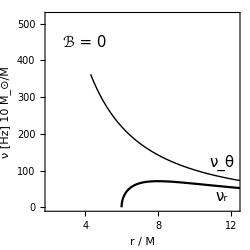
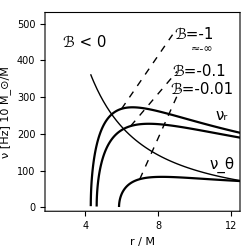
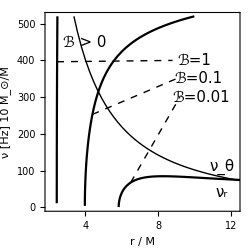

```mathematica
InfF[BB_,pos_,RR_]:={Black,Dashed,Line[{{RR,MAGprR[RR,BB,mm]},{pos[[1]]-1.2,pos[[2]]}}],Black,Text[Style[Framed[Row[{cb,"=",BB}],FrameStyle->White],fontyW],pos]};

{pic1=Show[
Plot[{SCHWprT[r,mm],If[r>6,SCHWprR[r,mm],Null]},{r,4.3,13},{PlotRange->mRange,PlotStyle->{{Black,Thick},{Black}},BaseStyle->15,
Frame->True,Axes->False,AspectRatio->1,ImageSize->ImSz,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,Epilog->{Text[Style[Framed[Row[{cb," = 0"}],RoundingRadius->5],fontyW],{4,450}],Text[Style["ν_r",15],{11.5,30}],Text[Style["ν_θ",15],{11.5,120}]}}]],

pic2=Plot[{MAGprT[r,0,mm],MAGprR[r,-0.01,mm],MAGprR[r,-0.1,mm],MAGprR[r,-1,mm]},{r,4.3,13},
{PlotRange->mRange,PlotStyle->{{Black,Thick},{Black},{Black},{Black}},BaseStyle->15,Frame->True,Axes->False,AspectRatio->1,ImageSize->ImSz,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,
Epilog->{Text[Style[Framed[Row[{cb," < 0"}],RoundingRadius->5],fontyW],{4,450}],Text[Style["ν_θ",15],{11.5,115}],Text[Style["ν_r",15],{11.5,250}],
InfF[-1,{10,470},6],Text["≈-∞",{10.4,430}],InfF[-0.1,{10.25,370},6.5],InfF[-0.01,{10.4,320},7]}}],

pic3=Plot[{MAGprT[r,0,mm],MAGprR[r,0.01,mm],MAGprR[r,0.1,mm],MAGprR[r,1,mm]},{r,2,13},{PlotRange->mRange,PlotStyle->{{Black,Thick},{Black},{Black},{Black}},BaseStyle->15,Frame->True,Axes->False,AspectRatio->1,ImageSize->ImSz,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,Epilog->{Text[Style[Framed[Row[{cb," > 0"}],RoundingRadius->5],fontyW],{4,450}],Text[Style["ν_θ",15],{11.5,110}],Text[Style["ν_r",15],{11.5,40}],
InfF[1,{10,400},2.46],InfF[0.1,{10.2,350},4.4],InfF[0.01,{10.4,300},6.5]}}]}
```

```mathematica
Export["10.eps",GraphicsRow[{pic1,pic2,pic3}]];
```

## fig. 10 ---/ frequencies at infinity /---

```mathematica
(* in physical units we have *)
```

```mathematica
mm=10;mRange={{2,12.3},{0,520}};aa1=0;aa2=0.5;aa3=0.99;

(* particle no mag. field *)
SCHWprK[r_,sol_]:=1/(2 Pi)c^3/(G sM sol)√(1/r^3);SCHWprT[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/r^3) ;SCHWprR[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((-6+r)/r^4);

(* string loop *)
SCHWloopT[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/r^3) ;SCHWloopR[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((3+(-5+r) r)/r^4);

(* charged particle *)
MAGprT[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/r^3);
MAGprR[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6-16 BB^3 r^3 √(-3+r (1+BB^2 (-2+r)^2 r))+8 BB^2 r^3 (-2+BB r √(-3+r (1+BB^2 (-2+r)^2 r))))/(r^4+4 BB^2 r^6));
MAGprP[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/(r^3 (1+2 BB r (BB (-2+r) r+√(-3+r (1+BB^2 (-2+r)^2 r))))));
MAGprL[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((16 BB^4 (-3+r)^2)/(r (-3+r-4 BB^2 r^2+2 BB^2 r^3-2 BB  √(r^2 (-3+r (1+BB^2 (-2+r)^2 r))))));
```

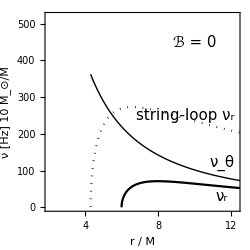
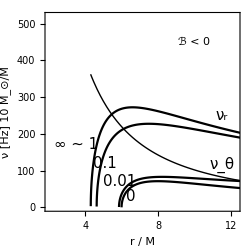
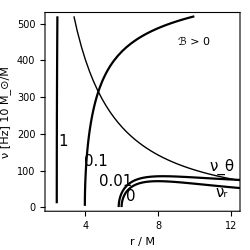

```mathematica
{pic1=Show[
Plot[{SCHWprT[r,mm],If[r>6,SCHWprR[r,mm],Null],SCHWloopR[r,mm]},{r,4.3,13},{PlotRange->mRange,PlotStyle->{{Black,Thick},{Black},{Black,Dotted}},BaseStyle->15,
Frame->True,Axes->False,AspectRatio->1,ImageSize->ImSz,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,Epilog->{Text[Style[Row[{cb," = 0"}],15],{10,450}],Text[Style["ν_r",15],{11.5,30}],Text[Style["ν_θ",15],{11.5,120}],Text[Style["string-loop ν_r",15],{9.5,250}]}}]],
pic2=Plot[{MAGprT[r,0,mm],MAGprR[r,0,mm],MAGprR[r,-0.01,mm],MAGprR[r,-0.1,mm],MAGprR[r,-1,mm]},{r,4.3,13},{PlotRange->mRange,PlotStyle->{{Black,Thick},{Black},{Black},{Black},{Black}},BaseStyle->15,Frame->True,Axes->False,AspectRatio->1,ImageSize->ImSz,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,Epilog->{Text[Row[{cb," < 0"}],{10,450}],Text[Style["ν_θ",15],{11.5,115}],Text[Style["ν_r",15],{11.5,250}],Text[Style["0",fontyW],{6.5,30}],Text[Style["0.01",fontyW],{5.9,70}],Text[Style["0.1",fontyW],{5.1,120}],Text[Style["∞ ∼ 1",fontyW],{3.5,170}]}}],
pic3=Plot[{MAGprT[r,0,mm],MAGprR[r,0,mm],MAGprR[r,0.01,mm],MAGprR[r,0.1,mm],MAGprR[r,1,mm]},{r,2,13},{PlotRange->mRange,PlotStyle->{{Black,Thick},{Black},{Black},{Black},{Black}},BaseStyle->15,Frame->True,Axes->False,AspectRatio->1,ImageSize->ImSz,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,Epilog->{Text[Row[{cb," > 0"}],{10,450}],Text[Style["ν_θ",15],{11.5,110}],Text[Style["ν_r",15],{11.5,40}],Text[Style["0",fontyW],{6.5,30}],Text[Style["0.01",fontyW],{5.7,70}],Text[Style["0.1",fontyW],{4.6,125}],Text[Style["1",fontyW],{2.8,180}],Text[Style["∞",fontyW],{1.5,220}]}}]}
```

```mathematica
Export["10.eps",GraphicsRow[{pic1,pic2,pic3}]];
```

## fig. 11 ---/ resonant radii and frequencies /---

```mathematica
MAGft2[r_,BB_]:= 1/r^3;MAGfr2[r_,BB_]:=(-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6-16 BB^3 r^3 √(-3+r (1+BB^2 (-2+r)^2 r))+8 BB^2 r^3 (-2+BB r √(-3+r (1+BB^2 (-2+r)^2 r))))/(r^4+4 BB^2 r^6);
```

```mathematica
rezRmn[BB_,m_,n_]:=(
Which[BB<0.5,point=5;,BB<1,point=5-BB;];
rez=Max[r/.FindRoot[m^2 MAGfr2[r,BB]==n^2 MAGft2[r,BB],{r,point}]];
If[rez<100,rez,0]
);

BB=0.1;
{rezRmn[-BB,3,2],rezRmn[-BB,2,3]}
{rezRmn[BB,3,2],rezRmn[BB,2,3]}
```

{5.3246,7.68569}

{4.34194,5.39805}

```mathematica
rezMN[r_,β_,M_,N_]:=M^2(-6+r+4 r^3 β^2 GG[r,β] +8 β^3 r^3(r-2) FF[r,β])-N^2 r(1+4 β^2 r^2);
XrezRmn[BB_,m_,n_]:=(
Max[Select[r/.NSolve[rezMN[r,BB,m,n]==0,r],Element[#,Reals]&]]
);
```

```mathematica
rezRmn[BB_,m_,n_]:=(
point=5;
rez=Max[r/.FindRoot[m^2 MAGfr2[r,BB]==n^2 MAGft2[r,BB],{r,point}]];
If[rez<100,rez,0]
);
{rezRmn[0.1,3,2],rezRmn[0.1,1,1],rezRmn[0.1,2,3]}
```

{4.34194,4.72287,5.39805}

```mathematica
Clear[InfoLine]
```

```mathematica
InfoLine[x0_,BB_,fU_,fD_]:={
Line[{{x0,fU[x0,BB,mm]},{x0,fD[x0,BB,mm]}}]
};
```

{6.,10.8,r11,r23}

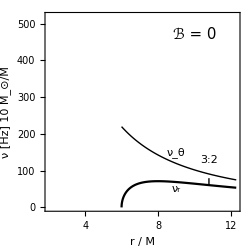

```mathematica
mm=10;y0=15;mRange={{2,12.3},{0,520}};VfontF=15;
RH2=2;BB=0;
start1=Max[Select[r/.NSolve[FceNull[r,BB]==0,r],Element[#,Reals]&]];
Quiet[r32=rezRmn[BB,3,2];
If[Element[r32,Reals]&&r32>RH2,mtext1={Text["3:2",{r32,130}],Line[{{r32,MAGprR[r32,BB,mm]},{r32,MAGprT[r32,BB,mm]}}]},mtext1=Null];
];
{start1,r32,r11,r23}

pic0=Plot[{MAGprR[r,BB,mm],MAGprT[r,BB,mm]},{r,start1,mRange[[1,2]]},PlotRange->mRange,PlotStyle->{{Black},{Black,Thick}},
Frame->True,Axes->False,AspectRatio->1,ImageSize->ImSz,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,
Epilog->{Text["ν_θ",{9,150}],Text["ν_r",{9,50}],Text[Style[Row[{cb," = ",BB}],{VfontF}],{10,470}],Dashed,mtext1},RegionFunction->Function[{x,y},x>RH2]]
```

{4.63195,5.3246,6.11469,7.68569}

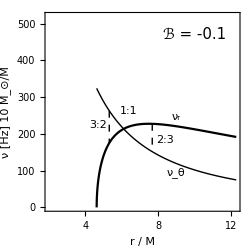

```mathematica
BB=-0.1;
start1=Max[Select[r/.NSolve[FceNull[r,BB]==0,r],Element[#,Reals]&]];
Quiet[r23=rezRmn[BB,2,3];r32=rezRmn[BB,3,2];r11=rezRmn[BB,1,1];
If[Element[r32,Reals]&&r32>RH2,mtext1={Text["3:2",{r32-0.6,MAGprR[r11,BB,mm]+10}],InfoLine[r32,BB,MAGprT,MAGprR]},mtext1=Null];
If[Element[r23,Reals]&&r23>RH2,mtext2={Text["2:3",{r23+0.7,MAGprT[r11,BB,mm]-30}],InfoLine[r23,BB,MAGprR,MAGprT]},mtext2=Null];
If[Element[r11,Reals]&&r11>RH2,mtext3={Text["1:1",{r11+0.3,MAGprT[r11,BB,mm]+50}]},mtext3=Null];
];
{start1,r32,r11,r23}

pic1=Plot[{MAGprR[r,BB,mm],MAGprT[r,BB,mm]},{r,start1,mRange[[1,2]]},PlotRange->mRange,PlotStyle->{{Black},{Black,Thick}},
Frame->True,Axes->False,AspectRatio->1,ImageSize->ImSz,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,
Epilog->{Text["ν_θ",{9,95}],Text["ν_r",{9,245}],Text[Style[Row[{cb," = ",BB}],{VfontF}],{10,470}],Dashed,mtext1,mtext2,mtext3,Black,Dotted},RegionFunction->Function[{x,y},x>RH2]]
```

{4.63195,4.34194,4.72287,5.39805}

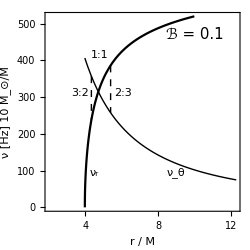

```mathematica
BB=0.1;
start2=Max[Select[r/.NSolve[FceNull[r,BB]==0,r],Element[#,Reals]&]];
Quiet[r23=rezRmn[BB,2,3];r32=rezRmn[BB,3,2];r11=rezRmn[BB,1,1];
If[Element[r32,Reals]&&r32>RH2,mtext1={Text["3:2",{r32-0.6,310}],InfoLine[r32,BB,MAGprT,MAGprR]},mtext1=Null];
If[Element[r23,Reals]&&r23>RH2,mtext2={Text["2:3",{r23+0.7,310}],InfoLine[r23,BB,MAGprR,MAGprT]},mtext2=Null];
If[Element[r11,Reals]&&r11>RH2,mtext3={Text["1:1",{r11+0.1,MAGprT[r11,BB,mm]+100}]},mtext3=Null];
];
{start1,r32,r11,r23}

pic2=Plot[{MAGprR[r,BB,mm],MAGprT[r,BB,mm]},{r,start2,mRange[[1,2]]},PlotRange->mRange,PlotStyle->{{Black},{Black,Thick}},
Frame->True,Axes->False,AspectRatio->1,ImageSize->ImSz,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,
Epilog->{Text["ν_θ",{9,95}],Text["ν_r",{4.5,95}],Text[Style[Row[{cb," = ",BB}],{VfontF}],{10,470}],Dashed,mtext1,mtext2,mtext3,Black,Dotted},RegionFunction->Function[{x,y},x>RH2]]
```

```mathematica
{pic0,pic1,pic2}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["11.eps",GraphicsRow[{pic0,pic1,pic2}]];
```

## fig. 12 ---/ explore fundamental frequencies /---

```mathematica
FF[r_,BB_]:=√(-3+r (1+BB^2 (-2+r)^2 r));GG[r_,β_]:=-4+r+8 r β^2-8 r^2 β^2+2 r^3 β^2;
fLL1[r_,BB_]:=(-BB r^2-r FF[r,BB])/(-3+r);fLL2[r_,BB_]:=(-BB r^2+r FF[r,BB])/(-3+r);
fceT[r_]:=1/r^3 ;
(* L < 0 *) OfceR1[r_,BB_]:=(-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6+16 BB^3 r^3 √(-3+r (1+BB^2 (-2+r)^2 r))-8 BB^2 r^3 (2+BB r √(-3+r (1+BB^2 (-2+r)^2 r))))/(r^4+4 BB^2 r^6);
(* L > 0 *) OfceR2[r_,BB_]:=(-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6-16 BB^3 r^3 √(-3+r (1+BB^2 (-2+r)^2 r))+8 BB^2 r^3 (-2+BB r √(-3+r (1+BB^2 (-2+r)^2 r))))/(r^4+4 BB^2 r^6);

(* L < 0 *) fceR1[r_,β_]:=(-6+r+4 r^3 β^2 GG[r,β] -8 β^3 r^3(r-2) FF[r,β])/(r^4(1+4 β^2 r^2));
(* L > 0 *) fceR2[r_,β_]:=(-6+r+4 r^3 β^2 GG[r,β] +8 β^3 r^3(r-2) FF[r,β])/(r^4(1+4 β^2 r^2));
{Simplify[OfceR1[r,BB]-fceR1[r,BB]],Simplify[OfceR2[r,BB]-fceR2[r,BB]]}
Simplify[{fceR1[r,0],fceR2[r,0]}]
```

{0.,0.}

{(-6+r)/r^4,(-6+r)/r^4}

```mathematica
rezMN1[r,-B,M,N]-rezMN2[r,B,M,N]
```

rezMN1[r,-B,M,N]-rezMN2[r,B,M,N]

```mathematica
rezMN1[r,B,M,N]-rezMN2[r,-B,M,N]
```

rezMN1[r,B,M,N]-rezMN2[r,-B,M,N]

```mathematica
rezMN1[r_,β_,M_,N_]:=M^2(-6+r+4 r^3 β^2 GG[r,β] -8 β^3 r^3(r-2) FF[r,β])-N^2 r(1+4 β^2 r^2);
rezMN2[r_,β_,M_,N_]:=M^2(-6+r+4 r^3 β^2 GG[r,β] +8 β^3 r^3(r-2) FF[r,β])-N^2 r(1+4 β^2 r^2);

ContR1[r_,β_]:=1/(√(-3+r (1+(-2+r)^2 r β^2)))(48 r^3 β^3-8 r^4 β^3-4 r^5 β^3+576 r^5 β^5-416 r^6 β^5+112 r^7 β^5-16 r^8 β^5-512 r^7 β^7+512 r^8 β^7-128 r^9 β^7+24 √(-3+r (1+(-2+r)^2 r β^2))-3 r √(-3+r (1+(-2+r)^2 r β^2))+144 r^2 β^2 √(-3+r (1+(-2+r)^2 r β^2))-4 r^3 β^2 √(-3+r (1+(-2+r)^2 r β^2))+160 r^5 β^4 √(-3+r (1+(-2+r)^2 r β^2))-16 r^6 β^4 √(-3+r (1+(-2+r)^2 r β^2))-256 r^6 β^6 √(-3+r (1+(-2+r)^2 r β^2))+128 r^7 β^6 √(-3+r (1+(-2+r)^2 r β^2)));

ContR2[r_,β_]:=1/(√(-3+r (1+(-2+r)^2 r β^2)))(-48 r^3 β^3+8 r^4 β^3+4 r^5 β^3-576 r^5 β^5+416 r^6 β^5-112 r^7 β^5+16 r^8 β^5+512 r^7 β^7-512 r^8 β^7+128 r^9 β^7+24 √(-3+r (1+(-2+r)^2 r β^2))-3 r √(-3+r (1+(-2+r)^2 r β^2))+144 r^2 β^2 √(-3+r (1+(-2+r)^2 r β^2))-4 r^3 β^2 √(-3+r (1+(-2+r)^2 r β^2))+160 r^5 β^4 √(-3+r (1+(-2+r)^2 r β^2))-16 r^6 β^4 √(-3+r (1+(-2+r)^2 r β^2))-256 r^6 β^6 √(-3+r (1+(-2+r)^2 r β^2))+128 r^7 β^6 √(-3+r (1+(-2+r)^2 r β^2)));

nullRR1[r_,β_]:=-6+r+4 r^3 β^2 GG[r,β] -8 β^3 r^3(r-2) FF[r,β];
nullRR2[r_,β_]:=-6+r+4 r^3 β^2 GG[r,β] +8 β^3 r^3(r-2) FF[r,β];
```

```mathematica
fontyW={FontSize->15,Background->LightGray}
```

{FontSize→15,Background→GrayLevel[0.85]}

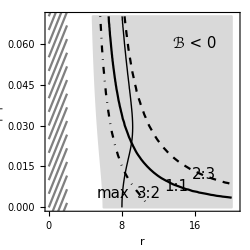

```mathematica
pic1=Show[RegionPlot[nullRR1[r,β]≥0,{r,3,20},{β,0,0.07},PlotStyle->{LightGray},BoundaryStyle->{LightGray},BaseStyle->15,FrameLabel->{"r",Row[{"|",cb,"|"}]},ImageSize->ImSz,RotateLabel->False,PlotRange->{{0,20.5},Automatic},Epilog->{Text[Style[Row[{cb," < 0"}],fontyW],{16,0.06}],Text[Style["max",fontyW],{7,0.005}],Text[Style["1:1",fontyW],{14,0.0077}],Text[Style["3:2",fontyW],{11,0.005}],Text[Style["2:3",fontyW],{17,0.012}]}],
ContourPlot[{ContR1[r,β]==0,rezMN1[r,β,2,3]==0,rezMN1[r,β,1,1]==0,rezMN1[r,β,3,2]==0},{r,0,20},{β,0,0.07},ContourStyle->{{Black,Thick},{Dashed,Black},{Black},{Black,DotDashed}}],
Plot[Table[x/120+b,{b,-0.1,0.07,0.005}],{x,0,2},{PlotStyle->{Gray}}]]
```

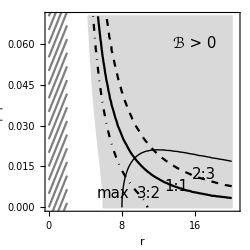

```mathematica
pic2=Show[RegionPlot[nullRR2[r,β]≥0,{r,3,20},{β,0,0.07},PlotStyle->{LightGray},BoundaryStyle->{LightGray},BaseStyle->15,FrameLabel->{"r",Row[{"|",cb,"|"}]},ImageSize->ImSz,RotateLabel->False,PlotRange->{{0,20.5},Automatic},Epilog->{Text[Style[Row[{cb," > 0"}],fontyW],{16,0.06}],Text[Style["max",fontyW],{7,0.005}],Text[Style["1:1",fontyW],{14,0.0077}],Text[Style["3:2",fontyW],{11,0.005}],Text[Style["2:3",fontyW],{17,0.012}]}],
ContourPlot[{ContR2[r,β]==0,rezMN2[r,β,2,3]==0,rezMN2[r,β,1,1]==0,rezMN2[r,β,3,2]==0},{r,0,20},{β,0,0.07},ContourStyle->{{Black,Thick},{Dashed,Black},{Black},{Black,DotDashed}}],
Plot[Table[x/120+b,{b,-0.1,0.07,0.005}],{x,0,2},{PlotStyle->{Gray}}]]
```

```mathematica
pic0=ContourPlot[{nullRR1[r,10^b]==0,nullRR2[r,10^b]==0},{r,2,7},{b,Log[10,0.001],Log[10,100]},PlotPoints->30,BaseStyle->15,ImageSize->ImSz,PlotRange->{{1.6,6.3},Automatic},FrameLabel->{"r",Row[{"|",cb,"|"}]},RotateLabel->False,ContourStyle->{{Thickness[0.02],LightGray},{Thickness[0.02],LightGray}},Epilog->{Text[Row[{cb," < 0"}],{5,1.5}],Text[Row[{cb," > 0"}],{2.7,1.5}],Dashed,Line[{{2,-3},{2,2}}],Line[{{rNull,-3},{rNull,2}}]},FrameTicks->{{Table[{y,ToString[Round[10^y,0.001]]},{y,Log[10,0.001],Log[10,100]}],Automatic},{Automatic,Automatic}}]
```

-Graphics-

```mathematica
Export["12.eps",GraphicsRow[{pic0,pic1,pic2}]];
```

```mathematica
Solve[3+(-5+r) r==0,r]
```

{{r→1/2 (5-√13)},{r→1/2 (5+√13)}}

```mathematica
rNull=1/2 (5+√13);N[rNull]
```

4.30278

```mathematica
TeXForm[1/2 (5+√13)]
```

\frac{1}{2} \left(5+\sqrt{13}\right)

## fig. 13 ---/ fitting QPOs /---

```mathematica
MAG1ft2[r_,BB_]:=1/r^3;MAG2ft2[r_,BB_]:=1/r^3;
MAG1fr2[r_,BB_]:=(-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6+16 BB^3 r^2 √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))-8 BB^2 r^3 (2+BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))))/(r^4+4 BB^2 r^6);
MAG2fr2[r_,BB_]:=(-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6-16 BB^3 r^2 √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))+8 BB^2 r^3 (-2+BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))))/(r^4+4 BB^2 r^6);

MAG1prT[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/r^3);MAG2prT[r_,BB_,sol_]:=MAG1prT[r,BB,sol];
MAG1prR[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6+16 BB^3 r^2 √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))-8 BB^2 r^3 (2+BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))))/(r^4+4 BB^2 r^6));
MAG2prR[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6-16 BB^3 r^2 √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))+8 BB^2 r^3 (-2+BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))))/(r^4+4 BB^2 r^6));
rezRmn1[BB_,m_,n_]:=(
Which[BB<0.5,point=5;,BB<1,point=5-BB;];
rez=Max[r/.FindRoot[m^2 MAG1fr2[r,BB]==n^2 MAG1ft2[r,BB],{r,point}]];
If[rez<100,rez,0]
);
rezRmn2[BB_,m_,n_]:=(
Which[BB<0.5,point=5;,BB<1,point=5-BB;];
rez=Max[r/.FindRoot[m^2 MAG2fr2[r,BB]==n^2 MAG2ft2[r,BB],{r,point}]];
If[rez<100,rez,0]
);
BB=0.1;
{rezRmn1[BB,3,2],rezRmn1[BB,2,3]}
{rezRmn2[BB,3,2],rezRmn2[BB,2,3]}
```

{5.3246,7.68569}

{4.34194,5.39805}

```mathematica
XrezRmn1[BB_,m_,n_]:=(
Max[Select[r/.NSolve[rezMN1[r,BB,m,n]==0,r],Element[#,Reals]&]]
);
XrezRmn2[BB_,m_,n_]:=(
Max[Select[r/.NSolve[rezMN2[r,BB,m,n]==0,r],Element[#,Reals]&]]
);
```

```mathematica
XTEf=Mean[{273,279}];QPO={XTEf,{0.29,0.52},{8.5,9.7}};

GROf=Mean[{447,453}];GRSf=Mean[{165,171}];
GROm={6.03,6.57};XTEm={8.5,9.7};GRSm={9.6,18.4};

MAGfce32[m_,BB_]:=(r32=XrezRmn[BB,3,2];MAGprT[r32,BB,m]);
MAGfce23[m_,BB_]:=(r23=XrezRmn[BB,2,3];MAGprR[r23,BB,m]);
```

```mathematica
MAG1fce32[m_,BB_]:=(r32=XrezRmn1[BB,3,2];MAG1prT[r32,BB,m]);
MAG1fce23[m_,BB_]:=(r23=XrezRmn1[BB,2,3];MAG1prR[r23,BB,m]);

MAG2fce32[m_,BB_]:=(r32=XrezRmn2[BB,3,2];MAG2prT[r32,BB,m]);
MAG2fce23[m_,BB_]:=(r23=XrezRmn2[BB,2,3];MAG2prR[r23,BB,m]);
```

```mathematica
BB=0;
{MAGfce23[10,BB],MAGfce23[10,BB]}
{MAGfce32[10,BB],MAGfce32[10,BB]}
```

{0.+460.864 ⅈ,0.+460.864 ⅈ}

{91.035,91.035}

```mathematica
BB2
```

-0.1

```mathematica
BBmin=0.063;BBmax=0.110;{XTEf,MAGfce32[XTEm[[1]],BBmin],MAGfce32[XTEm[[2]],BBmax]}
```

{276,337.684,384.743}

```mathematica
BBmin=0.041;BBmax=0.056;{XTEf,MAG2fce32[XTEm[[1]],BBmin],MAG2fce32[XTEm[[2]],BBmax]}
```

{276,274.765,279.652}

```mathematica
BBmin=0.113;BBmax=0.37;{XTEf,MAG1fce23[XTEm[[1]],BBmin],MAG1fce23[XTEm[[2]],BBmax]}
```

{276,275.928,276.103}

```mathematica
BBmin=0.048;BBmax=0.058;{XTEf,MAG2fce23[XTEm[[1]],BBmin],MAG2fce23[XTEm[[2]],BBmax]}
```

{276,275.525,276.327}

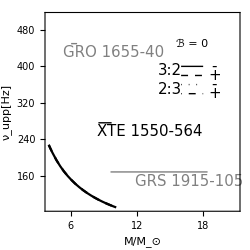

```mathematica
Clear[BB];
NiceFig[BB_]:=(
vUPr32MAG1=Table[{m,MAGfce32[m,-BB]},{m,4,21,1}];IvUPr32MAG1=Interpolation[vUPr32MAG1];
vUPr23MAG1=Table[{m,MAGfce23[m,-BB]},{m,4,21,1}];IvUPr23MAG1=Interpolation[vUPr23MAG1];
vUPr32MAG2=Table[{m,MAGfce32[m,BB]},{m,4,21,1}];IvUPr32MAG2=Interpolation[vUPr32MAG2];
vUPr23MAG2=Table[{m,MAGfce23[m,BB]},{m,4,21,1}];IvUPr23MAG2=Interpolation[vUPr23MAG2];

pic=Plot[{IvUPr32MAG1[m],IvUPr32MAG2[m],IvUPr23MAG1[m],IvUPr23MAG2[m]},{m,4,21},{PlotRange->{{4,21},{90,510}},Frame->True,BaseStyle->15,ImageSize->ImSz,Axes->False,FrameLabel->{Style[" M/M_⊙",{15,SingleLetterItalics->False}],Style[" ν_upp[Hz] ",15]},PlotStyle->{{Black},{Black,Dashed},{Black,Dotted},{Black,DotDashed}},AspectRatio->1,
Epilog->{
Gray,Thick,Line[{{GROm[[1]],GROf},{GROm[[2]],GROf}}],Line[{{GRSm[[1]],GRSf},{GRSm[[2]],GRSf}}],Black,Line[{{XTEm[[1]],XTEf},{XTEm[[2]],XTEf}}],
Text[Style["GRO 1655-40",VfontF,Gray],{GROm[[2]]+3.3,GROf-20}],Text[Style["XTE 1550-564",VfontF],{XTEm[[2]]+3.5,XTEf-20}],Text[Style["GRS 1915-105",VfontF,Gray],{GRSm[[2]]-1.7,GRSf-20}],
White,Thin,Polygon[{{14,320},{20,320},{20,420},{14,420}}],Black,Text[Framed[Row[{cb," = ",BB}]],{17,GROf}],
Text[Style["3:2",{VfontF}],{15,390}],Line[{{16,400},{18,400}}],Text[Style["-",{VfontF}],{19,400}],
Dashed,Line[{{16,380},{18,380}}],Text[Style["+",{VfontF}],{19,380}],
Text[Style["2:3",{VfontF}],{15,350}],Dotted,Line[{{16,360},{18,360}}],Text[Style["-",{VfontF}],{19,360}],
DotDashed,Line[{{16,340},{18,340}}],Text[Style["+",{VfontF}],{19,340}]}
}];

pic
);

NiceFig[0]
```

```mathematica
ImSz
```

250

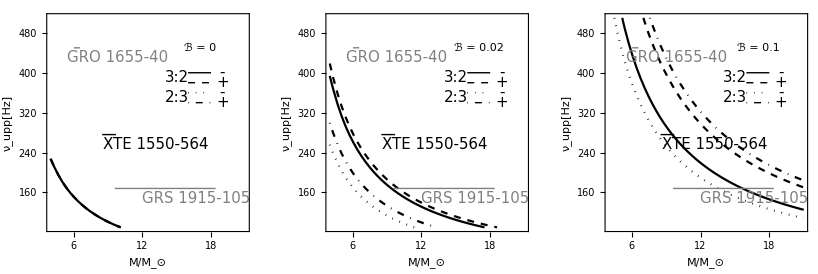

```mathematica
picB=GraphicsRow[{pic1=NiceFig[0],pic2=NiceFig[0.02],pic3=NiceFig[0.1]}]
```

```mathematica
Export["13.eps",picB];
```

## old old old fig. 10. ---/ frequencies at infinity /--- +++ Kepletian frequency +++

```mathematica
(* in physical units we have *)
```

```mathematica
mm=10;mRange={{2,12.3},{0,520}};aa1=0;aa2=0.5;aa3=0.99;

(* particle no mag. field *)
SCHWprK[r_,sol_]:=1/(2 Pi)c^3/(G sM sol)√(1/r^3);SCHWprT[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/r^3) ;SCHWprR[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((-6+r)/r^4);

(* string loop *)
SCHWloopT[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/r^3) ;SCHWloopR[r_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((3+(-5+r) r)/r^4);

(* charged particle *)
MAGprT[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/r^3);
MAGprR[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6-16 BB^3 r^3 √(-3+r (1+BB^2 (-2+r)^2 r))+8 BB^2 r^3 (-2+BB r √(-3+r (1+BB^2 (-2+r)^2 r))))/(r^4+4 BB^2 r^6));
MAGprP[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √(1/(r^3 (1+2 BB r (BB (-2+r) r+√(-3+r (1+BB^2 (-2+r)^2 r))))));
MAGprL[r_,BB_,sol_]:=1/(2 Pi)c^3/(G sM sol) √((16 BB^4 (-3+r)^2)/(r (-3+r-4 BB^2 r^2+2 BB^2 r^3-2 BB  √(r^2 (-3+r (1+BB^2 (-2+r)^2 r))))));
```

```mathematica
{(-6+r-32 BB^4 r^5+8 BB^4 r^6-16 BB^2 r^3 (1+BB √(-3+r (1+BB^2 (-2+r)^2 r)))+4 BB^2 r^4 (1+2 BB (4 BB+√(-3+r (1+BB^2 (-2+r)^2 r)))))/(r^4+4 BB^2 r^6),1/r^3,1/(r^3 (1+2 BB r (BB (-2+r) r+√(-3+r (1+BB^2 (-2+r)^2 r))))),(16 BB^4 (-3+r)^2)/(r (-3+r (1+2 BB^2 (-2+r) r-2 BB √(-3+r (1+BB^2 (-2+r)^2 r)))))}
```

{(-6+r-32 BB^4 r^5+8 BB^4 r^6-16 BB^2 r^3 (1+BB √(-3+r (1+BB^2 (-2+r)^2 r)))+4 BB^2 r^4 (1+2 BB (4 BB+√(-3+r (1+BB^2 (-2+r)^2 r)))))/(r^4+4 BB^2 r^6),1/r^3,1/(r^3 (1+2 BB r (BB (-2+r) r+√(-3+r (1+BB^2 (-2+r)^2 r))))),(16 BB^4 (-3+r)^2)/(r (-3+r (1+2 BB^2 (-2+r) r-2 BB √(-3+r (1+BB^2 (-2+r)^2 r)))))}

```mathematica
FceOBR[BB_]:=
{pic1=Show[
Plot[{SCHWprT[r,mm],If[r>6,SCHWprR[r,mm],Null],SCHWloopR[r,mm]},{r,4.3,13},{PlotRange->mRange,PlotStyle->{{Black,Thick},{Black},{Black,Dotted}},BaseStyle->15,
Frame->True,Axes->False,AspectRatio->1,ImageSize->300,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,Epilog->{Text[Style[Row[{cb," = 0"}],15],{10,450}],Text[Style["ν_r",15],{11.5,30}],Text[Style["ν_θ",15],{11.5,120}],Text[Style["string-loop ν_r",15],{10,250}]}}]],

pic2=Plot[{MAGprT[r,-BB,mm],MAGprR[r,-BB,mm],MAGprP[r,-BB,mm],MAGprL[r,-BB,mm]},{r,2,13},{PlotRange->mRange,PlotStyle->{{Black,Thick},{Black},{Black,Dashed},{Red,Dashed}},BaseStyle->15,Frame->True,Axes->False,AspectRatio->1,ImageSize->300,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,Epilog->{Text[Row[{cb," = ",-BB}],{10,450}],Text[Style["ν_θ",15],{11.5,115}],Text[Style["ν_r",15],{11.5,250}]}}],

pic3=Plot[{MAGprT[r,BB,mm],MAGprR[r,BB,mm],MAGprP[r,BB,mm],MAGprL[r,BB,mm]},{r,2,13},{PlotRange->mRange,PlotStyle->{{Black,Thick},{Black},{Black,Dashed},{Red,Dashed}},BaseStyle->15,Frame->True,Axes->False,AspectRatio->1,ImageSize->300,FrameLabel->{Row[{Style["r ",{15,Italic}],Style["/ M",15]}],Style["ν  [Hz]  10 M_⊙/M",{15,SingleLetterItalics->False}]},RotateLabel->True,BaseStyle->15,Epilog->{Text[Row[{cb," = ",BB}],{10,450}],Text[Style["ν_θ",15],{11.5,110}],Text[Style["ν_r",15],{11.5,40}]}}]
};
```

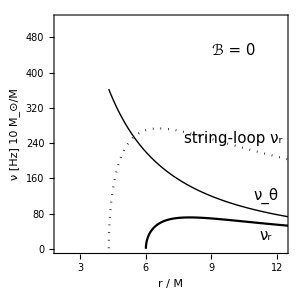
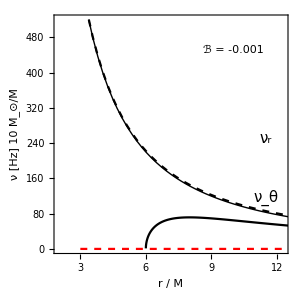
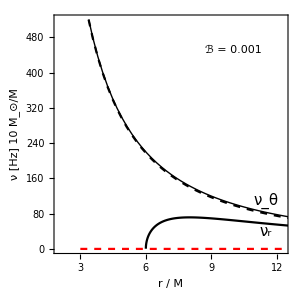

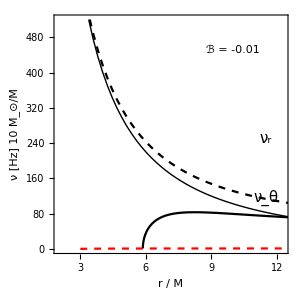
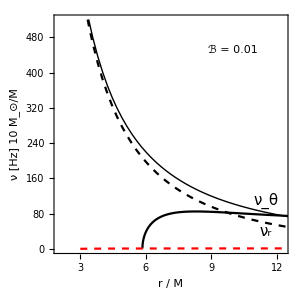
{-Graphics-,-Graphics-,-Graphics-}

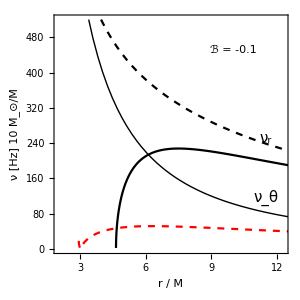
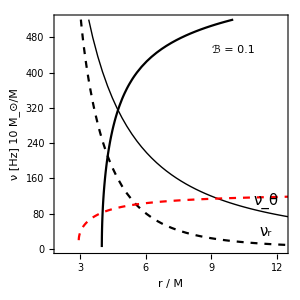
{-Graphics-,-Graphics-,-Graphics-}

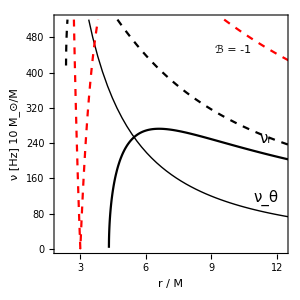
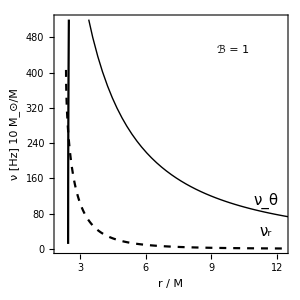
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
FceOBR[0.001]
FceOBR[0.01]
FceOBR[0.1]
FceOBR[1]
```

## frequency calculation > particle, SCHW, homo MAG field

```mathematica
1/gϕϕ(LL -BB gϕϕ)^2= gϕϕ 1/gϕϕ^2(LL -BB gϕϕ)^2=gϕϕ(LL/gϕϕ -BB)^2=x^2(LL/x^2 -BB)^2=(x LL/x^2 -x BB)^2=(LL/x - BB x)^2
```

Set::write: Tag Power in (18.0924/x-BB x)^2 is Protected.

Set::write: Tag Times in (-BB+18.0924/x^2)^2 x^2 is Protected.

Set::write: Tag Times in (-BB+18.0924/gϕϕ)^2 gϕϕ is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

(18.0924/x-BB x)^2

```mathematica
Clear[J2,E2,EE,LL,BB,θ,r,ω,a];
(* metric definition *)
AA[r_]:=(1-2/r); gtt[r_,θ_]:=-AA[r];grr[r_,θ_]:=1/AA[r];gθθ[r_,θ_]:= r^2;gϕϕ[r_,θ_]:=r^2 Sin[θ]^2;
(* Hamiltonian *)
(* H = Subscript[H, D](dynam. part) +  Subscript[H, P](potential part) *) 
Hpot[r_,θ_]=1/2+1/2( 1/gtt[r,θ] EE^2+1/gϕϕ[r,θ](LL -BB gϕϕ[r,θ])^2);
ωr2=1/grr[r,θ] D[(D[Hpot[r,θ], r]), r];ωθ2=1/gθθ[r,θ] D[(D[Hpot[r,θ], θ]), θ];
Simplify[{ωr2,ωθ2}]
```

{((BB^2 (-2+r)^3 r^4-2 EE^2 r^4 Csc[θ]^2+3 LL^2 (-2+r)^3 Csc[θ]^4) Sin[θ]^2)/((-2+r)^2 r^5),-BB^2+2 BB^2 Cos[θ]^2+(2 LL^2 Cot[θ]^2 Csc[θ]^2)/r^4+(LL^2 Csc[θ]^4)/r^4}

```mathematica
HpotX[r_,θ_]=1/2+1/2( 1/gtt[r,θ] EE^2+1/gϕϕ[r,θ](mLL)^2);(* <- WRONG     mLL is not a constant!!!
Xωr2=1/grr[r,θ] ∂_r (∂_r HpotX[r,θ]);Xωθ2=1/gθθ[r,θ]∂_θ (∂_θ HpotX[r,θ]);
θ=Pi/2;Simplify[{Xωr2,Xωθ2}]
```

```mathematica
θ=Pi/2;Simplify[{ωr2,ωθ2}]
```

{(3 LL^2 (-2+r))/r^5+(-2 EE^2+BB^2 (-2+r)^3)/((-2+r)^2 r),-BB^2+LL^2/r^4}

```mathematica
θ=Pi/2;Solve[1/2+1/2( 1/gtt[r,θ] E2+1/gϕϕ[r,θ](LL -BB gϕϕ[r,θ])^2)==0,E2]
```

{{E2→((-2+r) (LL^2+r^2-2 BB LL r^2+BB^2 r^4))/r^3}}

```mathematica
(* we must calcualte energy EE and angular momentum LL at circular orbit *)

Solve[1/2+1/2( 1/gtt[r,θ] E2+1/gϕϕ[r,θ](LL -BB gϕϕ[r,θ])^2)==0,E2]
```

{{E2→((-2+r) (LL^2+r^2-2 BB LL r^2+BB^2 r^4))/r^3}}

```mathematica
(* Energy boundary function *)
EB2[r_,θ_,LL_]:=((-2+r) (BB^2 r^4+r^2 Csc[θ]^2-2 BB LL r^2 Csc[θ]^2+LL^2 Csc[θ]^4) Sin[θ]^2)/r^3;
Simplify[D[EB2[r,Pi/2,LL], r]==0]
Simplify[Solve[D[EB2[r,Pi/2,LL], r]==0,LL]]
```

(LL^2 (-3+r))/r+2 BB LL r+BB^2 r^3==r+BB^2 r^4

{{LL→(r (-BB r+√(-3+r+4 BB^2 r^2-4 BB^2 r^3+BB^2 r^4)))/(-3+r)},{LL→-(r (BB r+√(-3+r+4 BB^2 r^2-4 BB^2 r^3+BB^2 r^4)))/(-3+r)}}

```mathematica
!!! There exist two solutions L<0 and L>0 !!! fLL2[r_,BB_]>0
```

True

```mathematica
fLL1[r_,BB_]:=(-BB r^2-√(-3 r^2+r^3+4 BB^2 r^4-4 BB^2 r^5+BB^2 r^6))/(-3+r);fLL2[r_,BB_]:=(-BB r^2+√(-3 r^2+r^3+4 BB^2 r^4-4 BB^2 r^5+BB^2 r^6))/(-3+r);
```

```mathematica
Clear[LL,EE,EB2];
```

```mathematica
FullSimplify[{ωr2,ωθ2}](* We must know the energy EE and momentum LL for particle at circular orbit. *)
```

{(3 LL^2 (-2+r))/r^5+(-2 EE^2+BB^2 (-2+r)^3)/((-2+r)^2 r),-BB^2+LL^2/r^4}

```mathematica
EE=√EB2[r,Pi/2,LL]
```

√EB2[r,π/2,LL]

```mathematica
(3 LL^2 (-2+r)r^2-2 (LL^2+r^2-2 BB LL r^2+BB^2 r^4)^2+BB^2 (-2+r)r^6)/r^5
```

(3 LL^2 (-2+r) r^2+BB^2 (-2+r) r^6-2 (LL^2+r^2-2 BB LL r^2+BB^2 r^4)^2)/r^5

```mathematica
(3 LL^2 (-2+r)r^2-2 (LL^2+r^2-2 BB LL r^2+BB^2 r^4)^2+BB^2 (-2+r)r^6)/r^5
```

(3 LL^2 (-2+r) r^2+BB^2 (-2+r) r^6-2 (LL^2+r^2-2 BB LL r^2+BB^2 r^4)^2)/r^5

```mathematica
Simplify[((r-2)/r^5(3 LL^2 +BB^2 r^4)-2(LL^2+r^2-2 BB LL r^2+BB^2 r^4)/((r-2) r^4))-(4 BB LL r^3+LL^2 (12-14 r+3 r^2)+r^3 (-2+BB^2 r (4-6 r+r^2)))/((-2+r) r^5)]
```

0

```mathematica
Clear[L,B]
TeXForm[((r-2)^2(3 L^2 +B^2 r^4)-2r(L^2+r^2-2 B L r^2+B^2 r^4))/((-2+r) r^5)]
```

\frac{(r-2)^2 \left(B^2 r^4+3 L^2\right)-2 r \left(B^2 r^4-2 B L r^2+L^2+r^2\right)}{(r-2) r^5}

```mathematica
\frac{(r-2)^2 \left(B^2 r^4+3 L^2\right)-2 r \left(B^2 r^4-2 B L r^2+L^2+r^2\right)}{(r-2) r^5}
```

Syntax::sntxb: Expression cannot begin with "\frac{(r-2)^2 \left(B^2 r^4+3 L^2\right)-2 r \left(B^2 r^4-2 B L r^2+L^2+r^2\right)}{(r-2) r^5}".

```mathematica
LL=(-BB r^2+r F)/(r-3);FullSimplify[{ωr2,ωθ2}]
```

{((-2+r) (3 F^2-6 BB F r+BB^2 r^2 (12+(-6+r) r)))/((-3+r)^2 r^3)-(2 EB2[r,π/2,(r (F-BB r))/(-3+r)])/((-2+r)^2 r),((F+BB (-4+r) r) (F-BB (-2+r) r))/((-3+r)^2 r^2)}

```mathematica
Simplify[{ωr2,ωθ2}]
```

{((-2+r) (3 F^2-6 BB F r+BB^2 r^2 (12-6 r+r^2)))/((-3+r)^2 r^3)-(2 EB2[r,π/2,(r (F-BB r))/(-3+r)])/((-2+r)^2 r),(F^2-2 BB F r-BB^2 r^2 (8-6 r+r^2))/((-3+r)^2 r^2)}

```mathematica
FullSimplify[{ωr2,ωθ2}]
```

{((-2+r) (3 F^2-6 BB F r+BB^2 r^2 (12+(-6+r) r)))/((-3+r)^2 r^3)-(2 EB2[r,π/2,(r (F-BB r))/(-3+r)])/((-2+r)^2 r),((F+BB (-4+r) r) (F-BB (-2+r) r))/((-3+r)^2 r^2)}

```mathematica
Symetry L>0 B>0  =  L<0 B<0 - we will take only one solution
```

Set::write: Tag Greater in L Symetry>0>0 is Protected.

L<0<-one only solution take we will

```mathematica
ωϕ2=(LL/gϕϕ[r,Pi/2]-BB)^2;ωL2=(4 BB^2)^2;
```

```mathematica
A)  L < 0
```

```mathematica
θ=Pi/2;
```

```mathematica
LL=fLL1[r,BB];EE=√EB2[r,Pi/2,LL];
(* now for local observer the frequencies *) FullSimplify[{ωr2,ωθ2,ωϕ2,ωL2}]
```

$Aborted

```mathematica
uUt2=(-1/gtt[r,Pi/2]EE)^2;Ωr2=ωr2/uUt2;Ωθ2=ωθ2/uUt2;Ωϕ2=ωϕ2/uUt2;ΩL2=ωL2/uUt2;
(* for observer at infinity *) FullSimplify[{Ωr2,Ωθ2,Ωϕ2,ΩL2}]
```

{((-9+3 r+24 BB^2 r^2-18 BB^2 r^3+4 BB^2 r^4+6 BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))) ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^3)/((-3+r)^2 r^2 EB2[r,π/2,-(BB r^2+√(r^2 (-3+r (1+BB^2 (-2+r)^2 r))))/(-3+r)])-((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)'[r])^2+1/2 (0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r] (0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)''[r],((-3+r-4 BB^2 r^2+2 BB^2 r^3+2 BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))) ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^2)/((-3+r)^2 r^2 EB2[r,π/2,-(BB r^2+√(r^2 (-3+r (1+BB^2 (-2+r)^2 r))))/(-3+r)]),((F-BB (-2+r) r)^2 ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^2)/((-3+r)^2 r^2 EB2[r,π/2,-(BB r^2+√(r^2 (-3+r (1+BB^2 (-2+r)^2 r))))/(-3+r)]),(16 BB^4 ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^2)/EB2[r,π/2,-(BB r^2+√(r^2 (-3+r (1+BB^2 (-2+r)^2 r))))/(-3+r)]}

```mathematica
FullSimplify[Solve[1/2+1/2( 1/gtt[r,θ] EE2+1/gϕϕ[r,θ](mLL)^2)==0,EE2],r>0]
```

{{EE2→((mLL^2+r^2) (0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])/r^2}}

```mathematica
MuUt2=(-1/gtt[r,Pi/2])^2((-2+r) (mLL^2+r^2))/r^3;
```

```mathematica
FullSimplify[1/MuUt2(mLL/gϕϕ[r,θ])^2]
```

(mLL^2 ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^2)/((-2+r) r (mLL^2+r^2))

```mathematica
mLL=fLL1[r,BB]-BB gϕϕ[r,θ];BB=0;FullSimplify[(mLL^2 (-2+r))/(r^3 (mLL^2+r^2))]
```

1/r^3

```mathematica
Clear[BB];mLL=fLL1[r,BB]-BB gϕϕ[r,θ];ΩK2=FullSimplify[(mLL^2 (-2+r))/(r^3 (mLL^2+r^2))]
```

(1+2 BB (BB (-2+r) r^2+√(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))))/(r^3+4 BB^2 r^5)

```mathematica
Clear[BB]
```

```mathematica
B)  L > 0
```

```mathematica
Clear[BB,LL,EE]
```

```mathematica
LL=fLL2[r,BB];EE=√EB2[r,Pi/2,LL];
(* now for local observer the frequencies *)  FullSimplify[{ωr2,ωθ2,ωϕ2,ωL2}]
```

{((-9+3 r+24 BB^2 r^2-18 BB^2 r^3+4 BB^2 r^4-6 BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))) (0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])/((-3+r)^2 r^2)+(EB2[r,π/2,(-BB r^2+√(r^2 (-3+r (1+BB^2 (-2+r)^2 r))))/(-3+r)] (-2 ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)'[r])^2+(0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r] (0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)''[r]))/(2 ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^2),(-3+r-4 BB^2 r^2+2 BB^2 r^3-2 BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r))))/((-3+r)^2 r^2),(F-BB (-2+r) r)^2/((-3+r)^2 r^2),16 BB^4}

```mathematica
uUt2=(-1/gtt[r,Pi/2]EE)^2;Ωr2=ωr2/uUt2;Ωθ2=ωθ2/uUt2;Ωϕ2=ωϕ2/uUt2;ΩL2=ωL2/uUt2;
(* for observer at infinity *) FullSimplify[{Ωr2,Ωθ2,Ωϕ2,ΩL2},r>2]
```

{((-9+r (3+2 BB^2 r (12+r (-9+2 r))-6 BB √(-3+r (1+BB^2 (-2+r)^2 r)))) ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^3)/((-3+r)^2 r^2 EB2[r,π/2,(r (-BB r+√(-3+r (1+BB^2 (-2+r)^2 r))))/(-3+r)])-((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)'[r])^2+1/2 (0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r] (0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)''[r],((-3+r (1+2 BB^2 (-2+r) r-2 BB √(-3+r (1+BB^2 (-2+r)^2 r)))) ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^2)/((-3+r)^2 r^2 EB2[r,π/2,(r (-BB r+√(-3+r (1+BB^2 (-2+r)^2 r))))/(-3+r)]),((F-BB (-2+r) r)^2 ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^2)/((-3+r)^2 r^2 EB2[r,π/2,(r (-BB r+√(-3+r (1+BB^2 (-2+r)^2 r))))/(-3+r)]),(16 BB^4 ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^2)/EB2[r,π/2,(r (-BB r+√(-3+r (1+BB^2 (-2+r)^2 r))))/(-3+r)]}

```mathematica
Reduce[r^3 (1+2 BB r (BB (-2+r) r+√(-3+r (1+BB^2 (-2+r)^2 r))))>0&&r>3]
```

BB∈ℝ&&r>3

```mathematica
BB=0;FullSimplify[{(-6+r)/r^4-Ωr2,1/r^3-Ωθ2}]
```

{(-6+r)/r^4-(3 ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^3)/((-3+r) r^2 EB2[r,π/2,r^2/(√((-3+r) r^2))])+((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)'[r])^2-1/2 (0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r] (0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)''[r],(1-(r ((0.02-84./(L/B)^(3/2)+(B^2 (60000. L-240000. B √(L/B)))/L^3)[r])^2)/((-3+r) EB2[r,π/2,r^2/(√((-3+r) r^2))]))/r^3}

```mathematica
mLL=fLL2[r,BB]-BB gϕϕ[r,θ];Clear[BB];FullSimplify[(mLL^2 (-2+r))/(r^3 (mLL^2+r^2))]
```

1/r^3

```mathematica
(-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6+16 BB^3 r^2 √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))-8 BB^2 r^3 (2+BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))))/(r^4+4 BB^2 r^6)
```

(-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6+16 BB^3 r^2 √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))-8 BB^2 r^3 (2+BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))))/(r^4+4 BB^2 r^6)

```mathematica
Fce1[BB_]:=(-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6+16 BB^3 r^2 √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))-8 BB^2 r^3 (2+BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))))/(r^4+4 BB^2 r^6);
Fce2[BB_]:=(-6+r+4 (BB^2+8 BB^4) r^4-32 BB^4 r^5+8 BB^4 r^6-16 BB^3 r^2 √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))+8 BB^2 r^3 (-2+BB √(r^2 (-3+r (1+BB^2 (-2+r)^2 r)))))/(r^4+4 BB^2 r^6);
{Simplify[Fce1[-B]-Fce2[B]],Simplify[Fce1[B]-Fce2[-B]]}
```

{0,0}

## old def>

```mathematica
FceRLmin[1]
```

FceRLmin[1]

{3.34745,3.05828}

```mathematica
LL=3;BB=0.1;√(LL/BB)
NSolve[EEstr[BB,LL]^2==EB2[r,Pi/2,BB,LL],r]
Sort[Select[r/.NSolve[EEstr[BB,LL]^2==EB2[r,Pi/2,BB,LL],r],Element[#,Reals]&]][[2]]
```

5.47723

{{r→-4.46163-3.84379 ⅈ},{r→-4.46163+3.84379 ⅈ},{r→5.47723},{r→2.72302-1.43566 ⅈ},{r→2.72302+1.43566 ⅈ}}

Part::partw: Part 2 of {5.47723} does not exist.

{5.47723}⟦2⟧

```mathematica
Simplify[Solve[EEstr[B,L]^2==EB2[r,Pi/2,B,L],B]]
```

{{B→L/r^2},{B→(-16 6^(2/3) L^2 r^10+24 6^(2/3) L^2 r^11-12 6^(2/3) L^2 r^12+2 6^(2/3) L^2 r^13+12 L^2 r^4 (9 L^2 (-2+r)^4 r^16+√3 √(-L^4 (-2+r)^8 r^30 (16 L^2 (-2+r)-27 r^2)))^(1/3)-12 L^2 r^5 (9 L^2 (-2+r)^4 r^16+√3 √(-L^4 (-2+r)^8 r^30 (16 L^2 (-2+r)-27 r^2)))^(1/3)+3 L^2 r^6 (9 L^2 (-2+r)^4 r^16+√3 √(-L^4 (-2+r)^8 r^30 (16 L^2 (-2+r)-27 r^2)))^(1/3)+6^(1/3) (9 L^2 (-2+r)^4 r^16+√3 √(-L^4 (-2+r)^8 r^30 (16 L^2 (-2+r)-27 r^2)))^(2/3))/(3 L (-2+r)^2 r^6 (9 L^2 (-2+r)^4 r^16+√3 √(-L^4 (-2+r)^8 r^30 (16 L^2 (-2+r)-27 r^2)))^(1/3))},{B→(ⅈ (ⅈ+√3) (9 L^2 (-2+r)^4 r^16+√3 √(-L^4 (-2+r)^8 r^30 (16 L^2 (-2+r)-27 r^2)))^(1/3))/(6^(2/3) L (-2+r)^2 r^6)+(L (2 (3 ⅈ 2^(2/3) 3^(1/6)+6^(2/3)) r^6-(3 ⅈ 2^(2/3) 3^(1/6)+6^(2/3)) r^7+3 (9 L^2 (-2+r)^4 r^16+√3 √(-L^4 (-2+r)^8 r^30 (16 L^2 (-2+r)-27 r^2)))^(1/3)))/(3 r^2 (9 L^2 (-2+r)^4 r^16+√3 √(-L^4 (-2+r)^8 r^30 (16 L^2 (-2+r)-27 r^2)))^(1/3))},{B→-(ⅈ (-ⅈ+√3) (9 L^2 (-2+r)^4 r^16+√3 √(-L^4 (-2+r)^8 r^30 (16 L^2 (-2+r)-27 r^2)))^(1/3))/(6^(2/3) L (-2+r)^2 r^6)+(L (2 (-3 ⅈ 2^(2/3) 3^(1/6)+6^(2/3)) r^6-(-3 ⅈ 2^(2/3) 3^(1/6)+6^(2/3)) r^7+3 (9 L^2 (-2+r)^4 r^16+√3 √(-L^4 (-2+r)^8 r^30 (16 L^2 (-2+r)-27 r^2)))^(1/3)))/(3 r^2 (9 L^2 (-2+r)^4 r^16+√3 √(-L^4 (-2+r)^8 r^30 (16 L^2 (-2+r)-27 r^2)))^(1/3))}}

## some calculations

```mathematica
Simplify[D[fLL1[r,BB], r]==0]
```

(BB r^2+√(r^2 (-3+r+4 BB^2 r^2-4 BB^2 r^3+BB^2 r^4))+(-3+r) (-2 BB r-((-2+r) r (3+2 BB^2 r^2 (-4+3 r)))/(2 √(r^2 (-3+r+4 BB^2 r^2-4 BB^2 r^3+BB^2 r^4)))))/(-3+r)^2==0

```mathematica
Simplify[D[(L[r]^2 (-3+r)+2 B L r^2+B^2 r^4-r^2-B^2 r^5), r]]
```

r (-2+4 B L+B^2 (4-5 r) r^2)+L[r]^2+2 (-3+r) L[r] L'[r]

```mathematica
Simplify[Solve[r (-2+4 B L+B^2 (4-5 r) r^2)+L^2==0,L]]
```

{{L→-2 B r-√(r (2+B^2 r (4-4 r+5 r^2)))},{L→-2 B r+√(r (2+B^2 r (4-4 r+5 r^2)))}}

### overeni vzorcu z clanku

```mathematica
FF[r_,BB_]:=√(BB^2 r^2 (-2+r)^2 +r-3);fLLnew[r_,BB_]:=(-BB r^2+r FF[r,BB])/(r-3);
Simplify[fLLnew[r,BB]-fLL[r,BB],r>0]
```

0

```mathematica
Simplify[(-BB r^2+r FF[r,BB])/(r-3)-(-BB r^2+r FF[r,BB])/(r-3)]
```

0

```mathematica
Simplify[{fLL1[r,BB]+fLL2[r,-BB],fLL2[r,BB]+fLL1[r,-BB]},r>0]
```

{0,0}

```mathematica
fISCO[r_,B_]:=6-r+2 B^2 r(12-8r+9 r^2-2 r^3)+2 B (-6+r) √(2r +B^2 r^2 (4-4 r+5 r^2))
```

### cosi

```mathematica
Clear[r,B]
FullSimplify[fLL[r,B]]
```

(-B r^2+√(r^2 (-3+r (1+B^2 (-2+r)^2 r))))/(-3+r)

```mathematica
Expand[(-3+r (1+B^2 (-2+r)^2 r)),r]
```

-3+r+4 B^2 r^2-4 B^2 r^3+B^2 r^4

```mathematica
Expand[(-3+r (1+B^2 (-2+r)^2 r)),B]
```

-3+r+B^2 (-2+r)^2 r^2

```mathematica
B^2 r^2(r-2)^2-3+r
```

-3+r+B^2 (-2+r)^2 r^2

```mathematica
(-B r^2+r √(-3+r (1+B^2 (-2+r)^2 r)))/(-3+r)
```

(-B r^2+r √(-3+r (1+B^2 (-2+r)^2 r)))/(-3+r)

```mathematica
Simplify[D[(-B r^2+r √(-3+r (1+B^2 (-2+r)^2 r)))/(-3+r), r]]
```

(18-9 r+r^2-48 B^2 r^2+68 B^2 r^3-30 B^2 r^4+4 B^2 r^5+12 B r √(-3+r (1+B^2 (-2+r)^2 r))-2 B r^2 √(-3+r (1+B^2 (-2+r)^2 r)))/(2 (-3+r)^2 √(-3+r (1+B^2 (-2+r)^2 r)))

```mathematica
Expand[18-9 r+r^2-48 B^2 r^2+68 B^2 r^3-30 B^2 r^4+4 B^2 r^5+12 B r  F-2 B r^2 F==0,B]
```

18-9 r+12 B F r+r^2-48 B^2 r^2-2 B F r^2+68 B^2 r^3-30 B^2 r^4+4 B^2 r^5==0

```mathematica
Simplify[18-9 r+12 B F r+r^2-48 B^2 r^2-2 B F r^2+68 B^2 r^3-30 B^2 r^4+4 B^2 r^5-(18-9 r+r^2+2 B F r(6-r)+2 B^2  r^2(2 r^3-15 r^2+34 r-24))]
```

0

```mathematica
-48 B^2 r^2+68 B^2 r^3-30 B^2 r^4
2 B^2  r^2(2 r^3-15 r^2+34 r-24)
```

-48 B^2 r^2+68 B^2 r^3-30 B^2 r^4

2 B^2 r^2 (-24+34 r-15 r^2+2 r^3)

```mathematica
18-9 r+r^2+2 B F r(6-r)-48 B^2 r^2+68 B^2 r^3-30 B^2 r^4+4 B^2 r^5==0
```

18-9 r+2 B F (6-r) r+r^2-48 B^2 r^2+68 B^2 r^3-30 B^2 r^4+4 B^2 r^5==0

```mathematica
18-9 r+12 B F r+r^2-48 B^2 r^2-2 B F r^2+B^2(68  r^3)-30 B^2 r^4+4 B^2 r^5==0
```

18-9 r+12 B F r+r^2-48 B^2 r^2-2 B F r^2+68 B^2 r^3-30 B^2 r^4+4 B^2 r^5==0

```mathematica
Simplify[18-9 r+r^2-48 B^2 r^2+68 B^2 r^3-30 B^2 r^4+4 B^2 r^5+12 B r  F-2 B r^2 F==0]
```

18+3 (-3+4 B F) r+(1-48 B^2-2 B F) r^2+68 B^2 r^3+4 B^2 r^5==30 B^2 r^4

```mathematica
FceNull[r,B]
```

FceNull[r,B]

```mathematica
-2B r( r-6)
```

-2 B (-6+r) r

```mathematica
18-9 r+r^2-48 B^2 r^2+68 B^2 r^3-30 B^2 r^4+4 B^2 r^5+12 B r-2 B r^2 √(-3+r (1+B^2 (-2+r)^2 r))==0
```

18-9 r+12 B r+r^2-48 B^2 r^2+68 B^2 r^3-30 B^2 r^4+4 B^2 r^5-2 B r^2 √(-3+r (1+B^2 (-2+r)^2 r))==0

```mathematica
Veff[r_,θ_,B_,L_]:=(1-2/r)(1+(L/(r Sin[θ])-B r Sin[θ])^2);
Simplify[EB2[r,θ,B,L]-Veff[r,θ,B,L]]
```

0

```mathematica
FullSimplify[D[Veff[r,θ,B,L], r]]
FullSimplify[D[Veff[r,θ,B,L], θ]]
```

(2-4 B L)/r^2-(2 L^2 (-3+r) Csc[θ]^2)/r^4+2 B^2 (-1+r) Sin[θ]^2

(2 (-2+r) (B^2 r^4 Cos[θ]-L^2 Cot[θ] Csc[θ]^3) Sin[θ])/r^3

### Solutions of (2)

```mathematica
(2 (-2+r) (B^2 r^4 Cos[θ]-L^2 Cot[θ] Csc[θ]^3) Sin[θ])/r^3==0
```

(2 (-2+r) (B^2 r^4 Cos[θ]-L^2 Cot[θ] Csc[θ]^3) Sin[θ])/r^3==0

```mathematica
Sin[θ]==0 ,=> θ==0
(-2+r)==0 ,=> r==2
B^2 r^4 Cos[θ]-L^2 Cot[θ] Csc[θ]^3==0
```

```mathematica
FullSimplify[Cos[θ](B^2 r^4 -L^2 1/Sin[θ]^4)-(B^2 r^4 Cos[θ]-L^2 Cot[θ] Csc[θ]^3)]
```

0

```mathematica
Cos[θ](B^2 r^4 -L^2 1/Sin[θ]^4) ,=>
Cos[θ],=> θ==Pi/2
B^2 r^4 Sin[θ]^4 -L^2 ==0 ,=>y==r Sin[θ],=>  y^2== L/B
```

### Solutions of (1)

```mathematica
θ=Pi/2;FullSimplify[(2-4 B L)/r^2-(2 L^2 (-3+r) Csc[θ]^2)/r^4+2 B^2 (-1+r) Sin[θ]^2]
```

2 B^2 (-1+r)-(2 L^2 (-3+r))/r^4+(2-4 B L)/r^2

```mathematica
Expand[2 B^2 (-1+r)r^4-2 L^2 (-3+r)+(2-4 B L)r^2,L]
```

-2 L^2 (-3+r)+2 r^2-4 B L r^2+2 B^2 (-1+r) r^4

```mathematica
Expand[2 B^2 (-1+r)r^4-2 L^2 (-3+r)+(2-4 B L)r^2==0,r]
```

6 L^2-2 L^2 r+(2-4 B L) r^2-2 B^2 r^4+2 B^2 r^5==0

```mathematica
Clear[L,B];Expand[-2EB2extr[r,B,L]==0,r]
```

6 L^2-2 L^2 r+2 r^2-4 B L r^2-2 B^2 r^4+2 B^2 r^5==0

```mathematica
Solve[EB2extr[r,B,L]==0,L]
```

{{L→(-B r^2-√(-3 r^2+r^3+4 B^2 r^4-4 B^2 r^5+B^2 r^6))/(-3+r)},{L→(-B r^2+√(-3 r^2+r^3+4 B^2 r^4-4 B^2 r^5+B^2 r^6))/(-3+r)}}

### off eq. extrema

```mathematica
Clear[r,θ];
```

```mathematica
AA=D[(D[Veff[r,θ,B,L], r]), r];
BB=D[(D[Veff[r,θ,B,L], θ]), r];
CC=D[(D[Veff[r,θ,B,L], θ]), θ];
```

### Lepsi koordinaty

```mathematica
Clear[x,y];(* x = r Sin[θ] *)
VeffX[x_,y_,B_,L_]:=(1-2/(√(x^2+y^2)))(1+(L/x-B x)^2);
D[VeffX[x,y,B,L], x]
D[VeffX[x,y,B,L], y]
```

(2 x (1+(L/x-B x)^2))/((x^2+y^2)^(3/2))+2 (-B-L/x^2) (L/x-B x) (1-2/(√(x^2+y^2)))

(2 (1+(L/x-B x)^2) y)/((x^2+y^2)^(3/2))

```mathematica
(L/x-B x)^2=-1;   nebo   y = 0
```

Set::write: Tag Power in (L/x-B x)^2 is Protected.

Set::write: Tag Times in nebo y is Protected.

0

```mathematica
Solve[(L/x-B x)^2==-1,x]
```

{{x→-(√(-1/B^2+(2 L)/B-(√(1-4 B L))/B^2))/(√2)},{x→(√(-1/B^2+(2 L)/B-(√(1-4 B L))/B^2))/(√2)},{x→-√(-1/(2 B^2)+L/B+(√(1-4 B L))/(2 B^2))},{x→√(-1/(2 B^2)+L/B+(√(1-4 B L))/(2 B^2))}}

```mathematica
L=-100;B=0.1;{(√(-1/B^2+(2 L)/B-(√(1-4 B L))/B^2))/(√2),√(-1/(2 B^2)+L/B+(√(1-4 B L))/(2 B^2))}
```

{0.+37.0156 ⅈ,0.+27.0156 ⅈ}

```mathematica
x=√(L/B);Simplify[(L/x-B x)]
```

0.-4.44089×10^-16 ⅈ

```mathematica
L=B x^2
```

-100.+0. ⅈ

```mathematica
1+(L/x-B x)^2==0
```

False

```mathematica
2 (L-B x^2) (L+B x^2) (1-2/(√(x^2+y^2)))==0
```

True

```mathematica
Clear[x,y];
y=0;Simplify[(2 x (1+(L/x-B x)^2))/((x^2+y^2)^(3/2))-(2 (L-B x^2) (L+B x^2) (1-2/(√(x^2+y^2))))/x^3==0]
```

(20000.-0.02 x^4-60000./(√(x^2))-42. √(x^2)+0.02 (x^2)^(3/2))/x^3==0

```mathematica
Expand[-2 B L x^2-L^2 (-3+x)+x^2 (1+B^2 (-x^2+x^3)),x]
```

(30000.+0. ⅈ)-(10000.+0. ⅈ) x+(21.+0. ⅈ) x^2-0.01 x^4+0.01 x^5

```mathematica
3 L^2- L^2 x+(1-2 B L)x^2- B^2 x^4+ B^2 x^5
```

(30000.+0. ⅈ)-(10000.+0. ⅈ) x+(21.+0. ⅈ) x^2-0.01 x^4+0.01 x^5

```mathematica
AA=D[(D[VeffX[x,y,B,L], x]), x];
BB=D[(D[VeffX[x,y,B,L], y]), x];
CC=D[(D[VeffX[x,y,B,L], y]), y];
```

General::ivar: 0 is not a valid variable.

```mathematica
Clear[x,y]; x=√(L/B) ;
({{AA, BB}, {BB, CC}})//MatrixForm
```

General::ivar: 0 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

(0.08+0.00493315 ⅈ | ∂_(0,0.+31.6228 ⅈ) (1.+0.0632456 ⅈ)
∂_(0,0.+31.6228 ⅈ) (1.+0.0632456 ⅈ) | ∂_0 ∂_0 (1.+0.0632456 ⅈ))

```mathematica
D[Veff[r,θ,B,L], r]
D[Veff[r,θ,B,L], θ]
```

2 (1-2/r) (((100.+0. ⅈ) Csc[θ])/r^2-0.1 Sin[θ]) (-((100.+0. ⅈ) Csc[θ])/r-0.1 r Sin[θ])+(2 (1+(-((100.+0. ⅈ) Csc[θ])/r-0.1 r Sin[θ])^2))/r^2

2 (1-2/r) (-0.1 r Cos[θ]+((100.+0. ⅈ) Cot[θ] Csc[θ])/r) (-((100.+0. ⅈ) Csc[θ])/r-0.1 r Sin[θ])

```mathematica
((L Csc[θ])/r-B r Sin[θ])
```

-((100.+0. ⅈ) Csc[θ])/r-0.1 r Sin[θ]

```mathematica
2 (1-2/r) (-B r Cos[θ]-(L Cot[θ] Csc[θ])/r) ((L Csc[θ])/r-B r Sin[θ])
```

2 (1-2/r) (-0.1 r Cos[θ]+((100.+0. ⅈ) Cot[θ] Csc[θ])/r) (-((100.+0. ⅈ) Csc[θ])/r-0.1 r Sin[θ])

```mathematica
1+(L/x-B x)^2==0
2 (-2+r) (-L^2+B^2 x^4)==0
```

False

(3.63798×10^-12+0. ⅈ) (-2+r)==0

```mathematica
L^2 (-3+r)+2 B L r^2+B^2 r^4-r^2-B^2 r^5;
```

### flat spc. a únik do nekonecna

```mathematica
Simplify[D[(1+(L/x-B x)^2), x]]
```

General::ivar: 0.+31.6228 ⅈ is not a valid variable.

∂_(0.+31.6228 ⅈ) (1.+0. ⅈ)

```mathematica
Solve[-2 L^2+2 B^2 x2^2==0,x2]
```

{{x2→-1000.},{x2→1000.}}

```mathematica
x=√(L/B);Simplify[(1+(L/x-B x)^2)]
```

1.+0. ⅈ

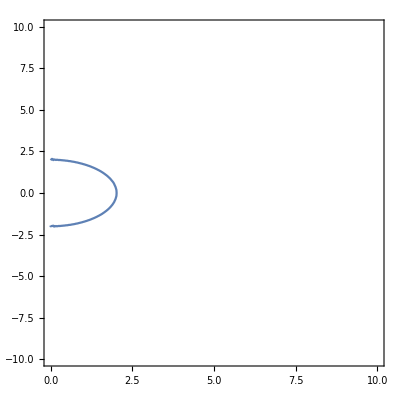

```mathematica
Clear[x,y];BB=0;LL=20;
ContourPlot[VeffX[x,y,BB,LL]==0.99,{x,0,10},{y,-10,10}]
```

```mathematica
Clear[x,y,L,B]
Limit[VeffX[√(L/-B),y,-B,-L],y->Infinity]
```

1-4 B L

```mathematica
Vflat[x_,B_,L_]:=(1+(L/x-B x)^2);
Simplify[D[Vflat[x,B,L], x]]
```

-(2 L^2)/x^3+2 B^2 x

```mathematica
x=√(L/B);Simplify[{Vflat[x,B,L],Vflat[x,-B,L]}]
x
```

{1,1+4 B L}

√(L/B)

```mathematica
√(LL/-BB)
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
LL=7;BB=0.4;Rmin=√(LL/BB);
{Vflat[Rmin,BB,LL],Vflat[Rmin,-BB,LL]}
```

{1.,12.2}

```mathematica
Clear[r];
FullSimplify[D[fLL[r,B], r]]
```

(B r^2-√(r^2 (-3+r (1+B^2 (-2+r)^2 r)))+(-3+r) (-2 B r+((-2+r) r (3+2 B^2 r^2 (-4+3 r)))/(2 √(r^2 (-3+r (1+B^2 (-2+r)^2 r))))))/(-3+r)^2

```mathematica
FullSimplify[B r^2 2 √(r^2 (-3+r (1+B^2 (-2+r)^2 r)))-2 r^2 (-3+r (1+B^2 (-2+r)^2 r))+(-3+r) (-2 B r2 √(r^2 (-3+r (1+B^2 (-2+r)^2 r)))+(-2+r) r (3+2 B^2 r^2 (-4+3 r)))]
```

-2 r^2 (-3+r (1+B^2 (-2+r)^2 r))+2 B r^2 √(r^2 (-3+r (1+B^2 (-2+r)^2 r)))+(-3+r) ((-2+r) r (3+2 B^2 r^2 (-4+3 r))-2 B √(r^2 (-3+r (1+B^2 (-2+r)^2 r))) r2)

```mathematica
Clear[r];
D[fLL[r,B], r]
```

(-2 B r+(-6 r+3 r^2+16 B^2 r^3-20 B^2 r^4+6 B^2 r^5)/(2 √(-3 r^2+r^3+4 B^2 r^4-4 B^2 r^5+B^2 r^6)))/(-3+r)-(-B r^2+√(-3 r^2+r^3+4 B^2 r^4-4 B^2 r^5+B^2 r^6))/(-3+r)^2

```mathematica
(-2 B r+(-6 r+3 r^2+16 B^2 r^3-20 B^2 r^4+6 B^2 r^5)/(2 √(-3 r^2+r^3+4 B^2 r^4-4 B^2 r^5+B^2 r^6)))/(-3+r)-(-B r^2+√(-3 r^2+r^3+4 B^2 r^4-4 B^2 r^5+B^2 r^6))/(-3+r)^2==0
```

(-2 B r+(-6 r+3 r^2+16 B^2 r^3-20 B^2 r^4+6 B^2 r^5)/(2 √(-3 r^2+r^3+4 B^2 r^4-4 B^2 r^5+B^2 r^6)))/(-3+r)-(-B r^2+√(-3 r^2+r^3+4 B^2 r^4-4 B^2 r^5+B^2 r^6))/(-3+r)^2==0